# NoteBook for Reissner - Nordstrom metric.

This notebook will compute the QNMs, potential and absorption probabilities for the Reissner - Nordstrom metric in any number of dimensions for spin - 3/2 fields. This notebook is coded to allow for multithreaded processing of the QNMs, this speeds up the amount of time take to compute all the QNMS.

## Setup

First clear global variables, then set up the number of iterations performed by the AIM, and finally define the mass of the black hole. We have always used m = 1.

```mathematica
Remove["Global`*"];
nmax=200; (*Number of iterations*)
TotM = 1;(*Black hole mass*)
TotΛ = 0; (* Asymtoptic curvature of space time*)
Names["Global`*"]
(* metric function*)
```

Remove::rmnsm: There are no symbols matching "Global`*".

{nmax,TotM,TotΛ}

## The Routines

### Seed table

First we setup the Seed table function which provides the seed values for the QNM calculations. It can also be used to determine the absorption probabilities. Inputs are, quantum numbers l and n, Charge and total number of dimensions of the metric. The format is the following
“WKBSeedTable[ElectricCharge, Number of Total Dimensions]”= {{l=0 and n=0},{l=1 and n=0, l=1 and n=1}, {l=2 and n=0,l=2 and n=1,l=2 and n=2},....}. The AIMSeed table follows the same format.

```mathematica
WKBSeed[l_,n_,TotQ_,TotDim_] := Module[{WKBSeedTable},
(*Charge = 0*)
WKBSeedTable[0,4]={{0.3112-0.0902ⅈ},{0.5300-0.0937ⅈ,0.5113-0.2854ⅈ},{0.7347-0.0948ⅈ,0.7210-0.2869ⅈ,0.6952-0.4855ⅈ},{0.9343-0.0953ⅈ,0.9235-0.2875ⅈ,0.9025-0.4839ⅈ,0.8732-0.6870ⅈ},{1.1315-0.0956ⅈ,1.1225-0.2879ⅈ,1.1049-0.4830ⅈ,1.0798-0.6829ⅈ,1.0484-0.8890ⅈ},{1.3273-0.0957ⅈ,1.3196-0.2881ⅈ,1.3045-0.4825ⅈ,1.2826-0.6805ⅈ,1.2547-0.8831ⅈ,1.2220-1.0914ⅈ}};
        WKBSeedTable[0,5]={{0.6563-0.2030ⅈ},{1.0688-0.2336ⅈ,0.9883-0.7176ⅈ},{1.4611-0.2404ⅈ,1.4000-0.7314ⅈ,1.2827-1.2541ⅈ},{1.8389-0.2436ⅈ,1.7895-0.7377ⅈ,1.6934-1.2526ⅈ,1.5568-1.8028ⅈ},{2.2089-0.2455ⅈ,2.1675-0.7413ⅈ,2.0860-1.2518ⅈ,1.9684-1.7873ⅈ,1.8206-2.3578ⅈ},{2.5745-0.2466ⅈ,2.5387-0.7435ⅈ,2.4681-1.2513ⅈ,2.3651-1.7777ⅈ,2.2334-2.3303ⅈ,2.0783-2.9162ⅈ}};
WKBSeedTable[0,6]={{0.9070-0.3487ⅈ},{1.5156-0.3538ⅈ,1.3359-1.0732ⅈ},{2.0273-0.3696ⅈ,1.8943-1.1246ⅈ,1.6223-1.9370ⅈ},{2.5198-0.3767ⅈ,2.4108-1.1426ⅈ,2.1910-1.9499ⅈ,1.8627-2.8391ⅈ},{3.0012-0.3808ⅈ,2.9086-1.1519ⅈ,2.7226-1.9532ⅈ,2.4440-2.8119ⅈ,2.0794-3.7618ⅈ},{3.4754-0.3835ⅈ,3.3949-1.1577ⅈ,3.2333- 1.9548ⅈ,2.9908-2.7943ⅈ,2.6708-3.7000ⅈ,2.2814-4.6993ⅈ}};
WKBSeedTable[0,7]={{1.2664-0.5107ⅈ},{1.9197-0.4761ⅈ,1.5584-1.4770ⅈ},{2.5270-0.4862ⅈ,2.2912-1.4719ⅈ,1.7655-2.5337ⅈ},{3.1009-0.4960ⅈ,2.9133-1.5006ⅈ,2.5148-2.5560ⅈ,1.8745-3.7439ⅈ},{3.6605-0.5022ⅈ,3.5011-1.5177ⅈ,3.1694-2.5731ⅈ,2.6457-3.7198ⅈ,1.9255-5.0393ⅈ},{4.2114-0.5063ⅈ,4.0720-1.5283ⅈ,3.7851-2.5817ⅈ,3.3369-3.7021ⅈ,2.7189-4.9454ⅈ,1.9421-6.3810ⅈ}};
WKBSeedTable[0,8]={{1.6674-0.6349ⅈ},{2.3282-0.6053ⅈ,1.8054-1.8887ⅈ},{2.9945-0.5999ⅈ,2.6179-1.8171ⅈ,1.7439-3.1635ⅈ},{3.6312-0.6065ⅈ,3.3415-1.8274ⅈ,2.6910-3.0971ⅈ,1.5750-4.5697ⅈ},{4.2500-0.6132ⅈ,4.0075-1.8474ⅈ,3.4822-3.1158ⅈ,2.5995-4.4984ⅈ,1.3242-6.1601ⅈ},{4.8583-0.6183ⅈ,4.6469-1.8626ⅈ,4.1984-3.1354ⅈ,3.4623-4.4873ⅈ,2.3948-6.0256ⅈ,1.0162-7.8869ⅈ}};
WKBSeedTable[0,9] ={{2.0765-0.7450ⅈ},{2.7570-0.7249ⅈ,2.0846-2.2240ⅈ},{3.4523-0.7123ⅈ,2.9269-2.1527ⅈ,1.6629-3.7424ⅈ},{4.1341-0.7127ⅈ,3.7206-2.1386ⅈ,2.7507-3.6014ⅈ,1.0045-5.3532ⅈ},{4.7990-0.7175ⅈ,4.4561-2.1516ⅈ,3.6831-3.5955ⅈ,2.2984-5.1611ⅈ,0.2204-7.1493ⅈ},{5.4524-0.7224ⅈ,5.1554-2.1680ⅈ,4.5054-3.6210ⅈ,3.3769-5.1372ⅈ,1.6471-6.9051ⅈ,-0.6311-9.1565ⅈ}};
WKBSeedTable[0,10] ={{ 2.0858-0.7392ⅈ},{2.7783-0.7238ⅈ,2.1521-2.2514ⅈ},{3.4633-0.7174ⅈ,2.9543-2.1949ⅈ,1.9533-3.8787ⅈ},{4.1365-0.7178ⅈ,3.7150-2.1780ⅈ,2.8575-3.7663ⅈ,1.6679-5.6051ⅈ},{4.7985-0.7209ⅈ,4.4407-2.1783ⅈ,3.7053-3.7170ⅈ,2.6359-5.4432ⅈ,1.3514-7.3913ⅈ},{5.4513-0.7245ⅈ,5.1406-2.1844ⅈ,4.5009-3.6989ⅈ,3.5460-5.3490ⅈ,2.3559-7.1932ⅈ,1.0141-9.2148ⅈ}};
(*Charge = 0.1*)
WKBSeedTable[0.1,4]={{0.3184-0.0909ⅈ},{0.5374-0.0942ⅈ,0.5191-0.2867ⅈ},{0.7424-0.0952ⅈ,0.7289-0.2878ⅈ,0.7034-0.4870ⅈ},{0.9424-0.0956ⅈ,0.9316-0.2883ⅈ,0.9109-0.4852ⅈ,0.8819-0.6887ⅈ},{1.1398-0.0958ⅈ,1.1309-0.2886ⅈ,1.1135-0.4842ⅈ,1.0886-0.6845ⅈ,1.0575-0.8909ⅈ},{1.3360-0.0960ⅈ,1.3283-0.2887ⅈ,1.3133-0.4835ⅈ,1.2916-0.6819ⅈ,1.2639-0.8848ⅈ,1.2315-1.0934ⅈ}};
        WKBSeedTable[0.1,5]= {{0.6484-0.2191ⅈ}, {1.0807-0.2343ⅈ,1.0008-0.7209ⅈ} ,{1.4742-0.2411ⅈ,1.4126-0.7342 ⅈ,1.2922-1.2636ⅈ},{1.8527-0.2443ⅈ,1.8040-0.7395ⅈ,1.7101-1.2546ⅈ,1.5787-1.8012ⅈ},{2.2232-0.2461ⅈ,2.1824-0.7429 ⅈ,2.1031-1.2534ⅈ,1.9911-1.7852ⅈ,1.8545-2.3415 ⅈ}, {2.5891-0.2471ⅈ,2.5536-0.7450ⅈ,2.4838-1.2536ⅈ,2.3822-1.7802ⅈ,2.2533-2.3315 ⅈ,2.1024-2.9129 ⅈ}};
        WKBSeedTable[0.1,6]={{0.94079-0.30272 ⅈ},{1.5292-0.3540 ⅈ,1.3680-1.0786ⅈ},{2.0418-0.3699ⅈ,1.9117-1.1279 ⅈ,1.6488-1.9502ⅈ},{2.5360-0.3772 ⅈ,2.4285-1.1444ⅈ,2.2124-1.9547ⅈ,1.8910-2.8487ⅈ},     {3.0183-0.3814ⅈ,2.9267-1.1537ⅈ,2.7428-1.9567ⅈ,2.4678-2.8176ⅈ,2.1087-3.7702ⅈ},{3.4932-0.3841ⅈ,3.4133-1.1596ⅈ,3.2531-1.9581ⅈ,3.0130-2.7991ⅈ,2.6964-3.7065ⅈ,2.3116-4.7073ⅈ}};
WKBSeedTable[0.1,7]={{1.2110-0.5136 ⅈ},{1.9388-0.4621ⅈ,1.6160-1.3961ⅈ},{2.5430-0.4836ⅈ,2.3243-1.4620ⅈ,1.8401-2.5026ⅈ},{3.1174-0.4954ⅈ,2.9352-1.5003ⅈ,2.5506-2.5600ⅈ,1.9395-3.7554ⅈ},{3.6784-0.5022ⅈ,3.5215-1.5186ⅈ,3.1959-2.5773ⅈ,2.6843-3.7312ⅈ,1.9854-5.0614ⅈ},{4.2305-0.5067ⅈ,4.0927-1.5296ⅈ,3.8092-2.5851ⅈ,3.3672-3.7097ⅈ,2.7597-4.9595ⅈ,1.9987-6.4037ⅈ}};
        WKBSeedTable[0.1,8]={{1.6037-0.6634 ⅈ},{2.3287-0.5875ⅈ,1.7906-1.8372ⅈ},{3.0099-0.5907 ⅈ,2.6599-1.7726ⅈ,1.8233-3.0215ⅈ},{3.6477-0.6031ⅈ,3.3727-1.8142ⅈ,2.7567-3.0604ⅈ,1.6923-4.4718ⅈ},{4.2677-0.6119 ⅈ,4.0320-1.8438ⅈ,3.5233-3.1106ⅈ,2.6731-4.4893ⅈ,1.4485-6.1367ⅈ},{4.8774-0.6179ⅈ,4.6696-1.8618ⅈ,4.2296-3.1365ⅈ,3.5100-4.4936ⅈ,2.4720-6.0399ⅈ,1.1375-7.9088ⅈ}};
WKBSeedTable[0.1,9] ={{2.0057-0.7926ⅈ},{2.7472-0.7096ⅈ,2.0442-2.2177ⅈ},{3.4606-0.6987ⅈ,2.9488-2.0939ⅈ,1.6851-3.5914ⅈ},{4.1486-0.7054ⅈ,3.7552-2.1058ⅈ,2.8252-3.5014ⅈ,1.0998-5.1043ⅈ},{4.8157-0.7139ⅈ,4.4856-2.1377ⅈ,3.7431-3.5587ⅈ,2.4086-5.0671ⅈ,0.3724-6.9500ⅈ},{5.4707-0.7206 ⅈ,5.1810-2.1623ⅈ,4.5486-3.6099ⅈ,3.4547-5.1152ⅈ,1.7778-6.8558ⅈ,-0.4388-9.0635ⅈ}};
(*Charge = 0.3 *)
WKBSeedTable[0.3,5]= {{0.6090-0.2537ⅈ},{1.0778-0.2335ⅈ,1.0020-0.7174ⅈ},{1.4712-0.2404ⅈ,1.4076-0.7335ⅈ,1.2782-1.2727ⅈ},{1.8503-0.2437ⅈ,1.8024-0.7375ⅈ,1.7114-1.2496ⅈ,1.5868-1.7871ⅈ},{2.2210-0.2455ⅈ,2.1804-0.7414ⅈ,2.1017-1.2509ⅈ,1.9908-1.7812ⅈ,1.8559-2.3350ⅈ},{2.5872-0.2467ⅈ,2.5519-0.7437ⅈ,2.4827-1.2512ⅈ,2.3831-1.7758ⅈ,2.2581-2.3221ⅈ,2.1142-2.8920ⅈ}};
(*Charge =0.4 *)
(*Charge = 0.5 *)
WKBSeedTable[0.5,4]={{0.3633 - 0.0952ⅈ},{0.5908-0.097ⅈ,0.5743-0.2948ⅈ},{0.8045-0.0975ⅈ,0.7922-0.2947ⅈ,0.7691-0.4976ⅈ},{1.0131-0.0977ⅈ,1.0033-0.2944ⅈ,0.9844-0.4950ⅈ,0.9579-0.7015ⅈ},{1.2193-0.0977ⅈ,1.2111-0.2942ⅈ,1.1951-0.4934ⅈ,1.1722-0.6967ⅈ,1.1436-0.9057ⅈ},{1.4240-0.0978ⅈ,1.4170-0.2940ⅈ,1.4031-0.4923ⅈ,1.3831-0.6937ⅈ,1.3576-0.8993ⅈ,1.3277-1.1101ⅈ}};        WKBSeedTable[0.5,5]={{0.8004-0.1499ⅈ},{1.1503-0.2346ⅈ,1.0842-0.7159ⅈ},{1.5519-0.2419ⅈ,1.4995-0.7345ⅈ,1.403-1.2505ⅈ},{1.9373-0.2448ⅈ,1.8930-0.7407ⅈ,1.8074-1.2558ⅈ,1.6868-1.8027ⅈ},{2.3145-0.2462ⅈ,2.2769-0.7431ⅈ,2.2035-1.2537ⅈ,2.0982-1.7871ⅈ,1.9669-2.3518ⅈ},{2.6867-0.2470ⅈ,2.6541-0.7443ⅈ,2.5901-1.2519ⅈ,2.4970-1.7765ⅈ,2.3787-2.3250ⅈ,2.2402-2.9032ⅈ}};
        WKBSeedTable[0.5,6]={{0.9545-0.1666ⅈ},{1.5411-0.3743ⅈ,1.2199-1.3800ⅈ},{2.1190 -0.3672ⅈ,2.0023-1.1224ⅈ,1.7720-1.9392ⅈ},{2.6235-0.3750ⅈ,2.5270-1.1383ⅈ,2.3350-1.9435ⅈ,2.0523-2.8251ⅈ},{3.1129-0.3795ⅈ,3.0295-1.1481ⅈ,2.8631-1.9468ⅈ,2.6165-2.8003ⅈ,2.2968-3.7377ⅈ},{3.5937-0.3822ⅈ,3.5203-1.1539ⅈ,3.3738-1.9481ⅈ,3.1555-2.7828ⅈ,2.8697-3.6795ⅈ,2.5246-4.6616ⅈ}};
WKBSeedTable[0.5,7]={{1.1967-0.3978ⅈ},{2.2696-0.4163ⅈ,3.6490-0.8740ⅈ},{2.5998-0.4897ⅈ,2.3449-1.6313ⅈ ,1.9354-3.3791ⅈ},{3.1984-0.4909ⅈ,3.0248-1.5096ⅈ,2.6649-2.6679ⅈ,2.1445-4.1160ⅈ},{3.7706-0.4975ⅈ,3.6269-1.5094ⅈ,3.3302-2.5804ⅈ,2.8719-3.7744ⅈ,2.2632-5.1748ⅈ},{4.3299-0.5025ⅈ,4.2034-1.5187ⅈ,3.9440-2.5725ⅈ,3.5428-3.7021ⅈ,2.9968-4.9618ⅈ,2.3192-6.4154ⅈ}};
        WKBSeedTable[0.5,8]={{1.5752-0.5955ⅈ},{2.3288-0.5151ⅈ,1.6814-1.5991ⅈ},{3.1584-0.5423ⅈ,3.3888-1.4247ⅈ,4.5018-1.5789ⅈ},{3.7291-0.5921ⅈ,3.5190-1.8260ⅈ,3.0966-3.2691ⅈ,2.5511-5.1747ⅈ},{4.3542-0.6034ⅈ,4.1414-1.8403ⅈ,3.6865-3.2022ⅈ,2.9873-4.8669ⅈ,2.1363-7.0381ⅈ},{4.9724-0.6106ⅈ,4.7820-1.8484ⅈ,4.3787-3.1498ⅈ,3.7330-4.6034ⅈ,2.8512-6.3454ⅈ,1.7971-8.5072ⅈ}};
WKBSeedTable[0.5,9] ={{2.0699-0.8973ⅈ},{2.2873-0.7099ⅈ,0.7367-4.1801ⅈ},{3.5719-0.5731ⅈ,3.5204-1.2536ⅈ,4.3912-0.0801ⅈ},{4.2559-0.6608ⅈ,4.1645-1.8651ⅈ,4.1861-2.5365ⅈ,5.1404-1.8769ⅈ},{4.9039-0.6945ⅈ,4.6654-2.0879ⅈ,4.1691-3.5076ⅈ,3.3873-5.0209ⅈ,2.3268-6.7583ⅈ},{5.5614-0.7079ⅈ,5.3103-2.1384ⅈ,4.7682-3.6368ⅈ,3.8827-5.3362ⅈ,2.6796-7.4582ⅈ,1.2929-10.1909ⅈ}};
       (*Charge = 1*)
       WKBSeedTable[1,4]={{0.5414-0.0864ⅈ},{0.8174-0.0873ⅈ,0.8032-0.2636ⅈ},{1.0811-0.0877ⅈ,1.0703-0.2642ⅈ,1.0490-0.4435ⅈ},{1.3395-0.0879ⅈ,1.3308-0.2645ⅈ,1.3135-0.4430ⅈ,1.2880-0.6245ⅈ},{1.5953-0.0881ⅈ,1.5880-0.2648ⅈ,1.5734-0.4427ⅈ,1.5517-0.6228ⅈ,1.5232-0.8060ⅈ},{1.8494-0.0882ⅈ,1.8431-0.2649ⅈ,1.8305-0.4425ⅈ,1.8117-0.6218ⅈ,1.7869-0.8034ⅈ,1.7563-0.9879ⅈ}};
        WKBSeedTable[1,5]= {{0.9218-0.1433ⅈ},{1.3413-0.2097ⅈ,1.2809-0.6422ⅈ},{1.7735-0.2147ⅈ,1.7266-0.6494ⅈ,1.6337-1.1014ⅈ},{2.1872-0.2175ⅈ,2.1486-0.6558ⅈ,2.0716-1.1049ⅈ,1.9574-1.5732ⅈ},{2.5917-0.2190ⅈ,2.5587-0.6594ⅈ,2.4929-1.1075ⅈ,2.3948-1.5691ⅈ,2.2655-2.0507ⅈ},{2.9908-0.2199ⅈ,2.9620-0.6616ⅈ,2.9045-1.1090ⅈ,2.8186-1.5665ⅈ,2.7049-2.0388ⅈ,2.5646-2.5311ⅈ}};
        WKBSeedTable[1,6]={{0.9027+0.0811ⅈ},{1.4904-0.4129ⅈ,0.7895-3.6637ⅈ},{2.3115-0.3240ⅈ,2.2297-0.9708ⅈ,2.0302-1.6426ⅈ},{2.8345-0.3368ⅈ,2.7554-1.0156 ⅈ,2.5948-1.7106ⅈ, 2.3449-2.4367ⅈ},{3.3438-0.3426ⅈ,3.2720-1.0332ⅈ,3.1269-1.7402ⅈ,2.9058-2.4774ⅈ,2.6054-3.2637ⅈ},{3.8435-0.3460ⅈ,3.7792-1.0422ⅈ,3.6494-1.7517ⅈ,3.4524-2.4854ⅈ,3.1862-3.2573ⅈ,2.8505-4.0854ⅈ}};
WKBSeedTable[1,7]={{1.8623-1.8256ⅈ},{2.2112-0.5279ⅈ,2.7539-1.8359ⅈ},{2.7749-0.4333ⅈ,2.7194-1.3659ⅈ,2.7162-2.4111ⅈ},{3.3883-0.4341ⅈ,3.3296-1.2462ⅈ,3.3425-1.7230ⅈ,3.9401-1.1831ⅈ},{3.9713-0.4516ⅈ,3.8600-1.3555ⅈ,3.6410-2.2421ⅈ,3.3018-3.0389ⅈ,2.7814-3.5851ⅈ},{4.5466-0.4595ⅈ,4.4389-1.3841ⅈ,4.2195-2.3230ⅈ,3.8773-3.2798ⅈ,3.3887-4.2548ⅈ,2.7165-5.2505ⅈ}};
        WKBSeedTable[1,8]={{1.5289-0.7460ⅈ},{2.2538+0.0072 ⅈ,2.1835-1.9362 ⅈ},{3.1760-0.4527ⅈ,2.8872-1.2827ⅈ,2.0722-1.9969ⅈ},{3.7084-0.6120ⅈ,2.5269-3.1149ⅈ,2.0045-9.2163ⅈ,2.275-19.104ⅈ},{4.5075-0.5588ⅈ,4.2157-1.7712ⅈ,3.4888-3.4778ⅈ,2.5501-6.3881ⅈ,1.8300-10.7389ⅈ},{5.1590-0.5631ⅈ,4.9803-1.7104ⅈ,4.5852-2.9378ⅈ,3.9193-4.3588ⅈ,2.9802-6.1488ⅈ,1.8535-8.4517ⅈ}};
WKBSeedTable[1,9] ={{2.0279-0.7437ⅈ},{1.4608-3.1750ⅈ,13.704-3.604ⅈ},{5.8738+0.2420ⅈ,13.8945+2.3400ⅈ,27.136+7.573ⅈ},{4.5357-0.6913ⅈ,6.3246-1.9357ⅈ,13.1054-2.6406ⅈ,27.624-3.435ⅈ},{4.9831-0.6896ⅈ,4.3785-2.6064ⅈ,3.6312-6.8145ⅈ,3.868-13.916ⅈ,4.854-24.572ⅈ},{5.7054-0.6677ⅈ,5.3489-2.1460ⅈ,4.4810-4.3852ⅈ,3.5612-8.3777ⅈ,3.151-14.379ⅈ,3.157-22.742ⅈ}};
Return[WKBSeedTable[TotQ,TotDim][[l+1,n+1]]]];
```

```mathematica
AIMSeed[l_,n_,TotQ_,TotDim_]:= Module[{AIMSeedTable},
(*Charge = 0*)
AIMSeedTable[0,4]={{0.3112-0.0902ⅈ},{0.5300-0.0937ⅈ,0.5113-0.2854ⅈ},{0.7347-0.0948ⅈ,0.7210-0.2869ⅈ,0.6952-0.4855ⅈ},{0.9343-0.0953ⅈ,0.9235-0.2875ⅈ,0.9025-0.4839ⅈ,0.8732-0.6870ⅈ},{1.1315-0.0956ⅈ,1.1225-0.2879ⅈ,1.1049-0.4830ⅈ,1.0798-0.6829ⅈ,1.0484-0.8890ⅈ},{1.3273-0.0957ⅈ,1.3196-0.2881ⅈ,1.3045-0.4825ⅈ,1.2826-0.6805ⅈ,1.2547-0.8831ⅈ,1.2220-1.0914ⅈ}};
        AIMSeedTable[0,5]={{0.6563-0.2030ⅈ},{1.0688-0.2336ⅈ,0.9883-0.7176ⅈ},{1.4611-0.2404ⅈ,1.4000-0.7314ⅈ,1.2827-1.2541ⅈ},{1.8389-0.2436ⅈ,1.7895-0.7377ⅈ,1.6934-1.2526ⅈ,1.5568-1.8028ⅈ},{2.2089-0.2455ⅈ,2.1675-0.7413ⅈ,2.0860-1.2518ⅈ,1.9684-1.7873ⅈ,1.8206-2.3578ⅈ},{2.5745-0.2466ⅈ,2.5387-0.7435ⅈ,2.4681-1.2513ⅈ,2.3651-1.7777ⅈ,2.2334-2.3303ⅈ,2.0783-2.9162ⅈ}};
AIMSeedTable[0,6]={{0.9070-0.3487ⅈ},{1.5156-0.3538ⅈ,1.3359-1.0732ⅈ},{2.0273-0.3696ⅈ,1.8943-1.1246ⅈ,1.6223-1.9370ⅈ},{2.5198-0.3767ⅈ,2.4108-1.1426ⅈ,2.1910-1.9499ⅈ,1.8627-2.8391ⅈ},{3.0012-0.3808ⅈ,2.9086-1.1519ⅈ,2.7226-1.9532ⅈ,2.4440-2.8119ⅈ,2.0794-3.7618ⅈ},{3.4754-0.3835ⅈ,3.3949-1.1577ⅈ,3.2333- 1.9548ⅈ,2.9908-2.7943ⅈ,2.6708-3.7000ⅈ,2.2814-4.6993ⅈ}};
AIMSeedTable[0,7]={{1.2664-0.5107ⅈ},{1.9197-0.4761ⅈ,1.5584-1.4770ⅈ},{2.5270-0.4862ⅈ,2.2912-1.4719ⅈ,1.7655-2.5337ⅈ},{3.1009-0.4960ⅈ,2.9133-1.5006ⅈ,2.5148-2.5560ⅈ,1.8745-3.7439ⅈ},{3.6605-0.5022ⅈ,3.5011-1.5177ⅈ,3.1694-2.5731ⅈ,2.6457-3.7198ⅈ,1.9255-5.0393ⅈ},{4.2114-0.5063ⅈ,4.0720-1.5283ⅈ,3.7851-2.5817ⅈ,3.3369-3.7021ⅈ,2.7189-4.9454ⅈ,1.9421-6.3810ⅈ}};
AIMSeedTable[0,8]={{1.6674-0.6349ⅈ},{2.3282-0.6053ⅈ,1.8054-1.8887ⅈ},{2.9945-0.5999ⅈ,2.6179-1.8171ⅈ,1.7439-3.1635ⅈ},{3.6312-0.6065ⅈ,3.3415-1.8274ⅈ,2.6910-3.0971ⅈ,1.5750-4.5697ⅈ},{4.2500-0.6132ⅈ,4.0075-1.8474ⅈ,3.4822-3.1158ⅈ,2.5995-4.4984ⅈ,1.3242-6.1601ⅈ},{4.8583-0.6183ⅈ,4.6469-1.8626ⅈ,4.1984-3.1354ⅈ,3.4623-4.4873ⅈ,2.3948-6.0256ⅈ,1.0162-7.8869ⅈ}};
AIMSeedTable[0,9] ={{2.0765-0.7450ⅈ},{2.7570-0.7249ⅈ,2.0846-2.2240ⅈ},{3.4523-0.7123ⅈ,2.9269-2.1527ⅈ,1.6629-3.7424ⅈ},{4.1341-0.7127ⅈ,3.7206-2.1386ⅈ,2.7507-3.6014ⅈ,1.0045-5.3532ⅈ},{4.7990-0.7175ⅈ,4.4561-2.1516ⅈ,3.6831-3.5955ⅈ,2.2984-5.1611ⅈ,0.2204-7.1493ⅈ},{5.4524-0.7224ⅈ,5.1554-2.1680ⅈ,4.5054-3.6210ⅈ,3.3769-5.1372ⅈ,1.6471-6.9051ⅈ,-0.6311-9.1565ⅈ}};
AIMSeedTable[0,10] ={{ 2.0858-0.7392ⅈ},{2.7783-0.7238ⅈ,2.1521-2.2514ⅈ},{3.4633-0.7174ⅈ,2.9543-2.1949ⅈ,1.9533-3.8787ⅈ},{4.1365-0.7178ⅈ,3.7150-2.1780ⅈ,2.8575-3.7663ⅈ,1.6679-5.6051ⅈ},{4.7985-0.7209ⅈ,4.4407-2.1783ⅈ,3.7053-3.7170ⅈ,2.6359-5.4432ⅈ,1.3514-7.3913ⅈ},{5.4513-0.7245ⅈ,5.1406-2.1844ⅈ,4.5009-3.6989ⅈ,3.5460-5.3490ⅈ,2.3559-7.1932ⅈ,1.0141-9.2148ⅈ}};
(*Charge = 0.1*)
AIMSeedTable[0.1,4]={{0.3188-0.1002ⅈ},{0.5376-0.0976ⅈ,0.5252-0.2999ⅈ},{0.7425-0.0970ⅈ,0.7315-0.2954ⅈ,0.7160-0.5030ⅈ},{0.9424-0.0967ⅈ,0.9329-0.2932ⅈ,0.9178-0.4967ⅈ,0.9019-0.7077ⅈ}, {1.1399-0.0966ⅈ,1.1317-0.2919ⅈ,1.1177-0.4927ⅈ,1.1014-0.7000ⅈ,1.0856-0.9131ⅈ},{1.3360-0.0965ⅈ,1.3288-0.2912ⅈ,1.3160-0.4900ⅈ,1.3001-0.6945ⅈ,1.2836-0.9044ⅈ,1.2682-1.1188ⅈ}};
AIMSeedTable[0.1,5]= {{0.6502-0.2536ⅈ},{1.0809-0.2504ⅈ,1.0361-0.7839ⅈ},{1.4744-0.2500ⅈ,1.4304-0.7733ⅈ,1.3803-1.3356ⅈ},{1.8527-0.2500ⅈ,1.8128-0.7665ⅈ,1.7581-1.3174ⅈ,1.7116-1.8944ⅈ}, {2.2232-0.2500ⅈ,2.1875-0.7623ⅈ,2.1329-1.3030ⅈ,2.0794-1.8712ⅈ,2.0369-2.4559ⅈ},{2.5891-0.2500ⅈ,2.5571-0.7594ⅈ,2.5047-1.2923ⅈ,2.4480-1.8511ⅈ,2.3982-2.4294ⅈ,2.3590-3.0186ⅈ}};       AIMSeedTable[0.1,6]={{0.9628-0.4089ⅈ}, {1.5247-0.3916ⅈ,1.4347-1.2486ⅈ},{2.0415-0.3899ⅈ,1.9514-1.2237ⅈ,1.8622-2.1373ⅈ},{2.5360-0.3901ⅈ,2.4520-1.2104ⅈ,2.3490-2.1058ⅈ,2.2733-3.0463ⅈ}, {3.0184-0.3905ⅈ,2.9416-1.2021ⅈ,2.8341-2.0795ⅈ,2.7415-3.0097ⅈ,2.6767-3.9633ⅈ},{3.4933-0.3908ⅈ,3.4234-1.1965ⅈ,3.3166-2.0585ⅈ,3.2130-2.9747ⅈ,3.1326-3.9229ⅈ,3.0756-4.8835ⅈ}};
AIMSeedTable[0.1,7]={{1.3123-0.5551ⅈ},{1.9415-0.5267ⅈ,1.7939-1.7102ⅈ},{2.5410-0.5192ⅈ,2.3927-1.6544ⅈ,2.2603-2.9188ⅈ}, {3.1170-0.5178ⅈ,2.9777-1.6262ⅈ,2.8209-2.8611ⅈ,2.7174-4.1581ⅈ}, {3.6785-0.5179ⅈ,3.5499-1.6101ⅈ,3.3819-2.8169ⅈ,3.2512-4.1023ⅈ,3.1676-5.4136ⅈ},{4.2306-0.5184ⅈ,4.1124-1.5999ⅈ,3.9417-2.7820ⅈ,3.7906-4.0501ⅈ,3.6836-5.3585ⅈ,3.6131-6.6772ⅈ}};       AIMSeedTable[0.1,8]={{1.6900-0.6861ⅈ},{2.3593-0.6549ⅈ,2.1465-2.1596ⅈ},{3.0132-0.6416ⅈ,2.7966-2.0738ⅈ,2.6183-3.6918ⅈ},{3.6477-0.6370ⅈ,3.4429-2.0248ⅈ,3.2277-3.5997ⅈ,3.0976-5.2513ⅈ}, {4.2678-0.6357ⅈ,4.0776-1.9963ⅈ,3.8431-3.5302ⅈ,3.6754-5.1677ⅈ,3.5754-6.8301ⅈ},{4.8776-0.6357ⅈ,4.7018-1.9784ⅈ,4.4598-3.4763ⅈ,4.2617-5.0931ⅈ,4.1315-6.7545ⅈ,4.0500-8.4218ⅈ}};
AIMSeedTable[0.1,9]={{2.0848-0.8056ⅈ},{2.7847-0.7745ⅈ,2.4989-2.5893ⅈ},{3.4757-0.7574ⅈ,3.1837-2.4807ⅈ,2.9572-4.4512ⅈ},{4.1528-0.7496ⅈ,3.8739-2.4108ⅈ,3.5974-4.3269ⅈ,3.4416-6.3317ⅈ}, {4.8171-0.7464ⅈ,4.5567-2.3671ⅈ,4.2510-4.2290ⅈ,4.0479-6.2177ⅈ,3.9331-8.2275ⅈ},{5.4715-0.7452ⅈ,5.2297-2.3391ⅈ,4.9102-4.1521ⅈ,4.6663-6.1169ⅈ,4.5156-8.1270ⅈ,4.4248-10.1369ⅈ}};
(*Charge = 0.5 *)
AIMSeedTable[0.5,4]={{0.3637-0.1031ⅈ},{0.5909-0.1000ⅈ,0.5794-0.3062ⅈ},{0.8046-0.0991ⅈ,0.7944-0.3013ⅈ,0.7796-0.5117ⅈ},{1.0132-0.0987ⅈ,1.0044-0.2987ⅈ,0.9902-0.5051ⅈ,0.9747-0.7184ⅈ}, {1.2193-0.0984ⅈ,1.2117-0.2972ⅈ,1.1986-0.5009ⅈ,1.1829-0.7105ⅈ,1.1675-0.9256ⅈ},{1.4240-0.0983ⅈ,1.4174-0.2963ⅈ,1.4054-0.4980ⅈ,1.3903-0.7048ⅈ,1.3742-0.9168ⅈ,1.3590-1.1331ⅈ}};
AIMSeedTable[0.5,5]={{0.7105-0.2391ⅈ},{1.1499-0.2490ⅈ,1.1093-0.7744ⅈ},{1.5518-0.2500ⅈ,1.5115-0.7700ⅈ,1.4632-1.3257ⅈ},{1.9374-0.2500ⅈ,1.9006-0.7646ⅈ,1.8487-1.3101ⅈ,1.8027-1.8810ⅈ}, {2.3145-0.2498ⅈ,2.2816-0.7604ⅈ,2.2302-1.2966ⅈ,2.1783-1.8586ⅈ,2.1357-2.4372ⅈ},{2.6867-0.2497ⅈ,2.6572-0.7574ⅈ,2.6081-1.2861ⅈ,2.5537-1.8389ⅈ,2.5047-2.4107ⅈ,2.4651-2.9937ⅈ}};
AIMSeedTable[0.5,6]={{0.9986-0.3374ⅈ},{1.5936-0.3722ⅈ,1.5258-1.1662ⅈ},{2.1206-0.3829ⅈ,2.0423-1.1929ⅈ,1.9591-2.0726ⅈ},{2.6237-0.3865ⅈ,2.5476-1.1941ⅈ,2.4506-2.0690ⅈ,2.3755-2.9881ⅈ}, {3.1129-0.3879ⅈ,3.0423-1.1909ⅈ,2.9408-2.0533ⅈ,2.8501-2.9662ⅈ,2.7844-3.9037ⅈ},{3.5937-0.3886ⅈ,3.5289-1.1873ⅈ,3.4281-2.0370ⅈ,3.3276-2.9380ⅈ,3.2472-3.8710ⅈ,3.1889-4.8177ⅈ}};
AIMSeedTable[0.5,7]={{1.2444-0.5240ⅈ},{1.9836-0.4901ⅈ,1.8538-1.5734ⅈ},{2.6112-0.5006ⅈ,2.4851-1.5782ⅈ,2.3620-2.7675ⅈ},{3.2002-0.5076ⅈ,3.0768-1.5840ⅈ,2.9305-2.7717ⅈ,2.8279-4.0212ⅈ}, {3.7707-0.5113ⅈ,3.6537-1.5832ⅈ,3.4959-2.7578ⅈ,3.3675-4.0082ⅈ,3.2823-5.2872ⅈ},{4.3298-0.5134ⅈ,4.2206-1.5803ⅈ,4.0595-2.7383ⅈ,3.9121-3.9781ⅈ,3.8043-5.2596ⅈ,3.7316-6.5538ⅈ}};
AIMSeedTable[0.5,8]={{1.2952-0.8322ⅈ},{2.1208-0.6897ⅈ,1.5397-2.8503ⅈ},{2.8881-0.6516ⅈ,2.2258-2.5367ⅈ,1.9221-4.8959ⅈ},{3.5756-0.6442ⅈ,2.9089-2.3759ⅈ,2.4418-4.7173ⅈ,2.2774-7.0808ⅈ}, {4.2280-0.6422ⅈ,3.5854-2.2721ⅈ,2.9815-4.5540ⅈ,2.7267-6.9712ⅈ,2.6186-9.3330ⅈ},{4.8613-0.6412ⅈ,4.2552-2.1979ⅈ,3.5534-4.3866ⅈ,3.1947-6.8308ⅈ,3.0352-9.2439ⅈ,2.9547-11.6059ⅈ}};   
AIMSeedTable[0.5,9] ={{1.9903-0.8005ⅈ},{2.7457-0.7514ⅈ,2.4325-2.5446ⅈ},{3.4940-0.7302ⅈ,3.2004-2.3915ⅈ,2.9617-4.3071ⅈ},{4.2052-0.7274ⅈ,3.9418-2.3281ⅈ,3.6667-4.1712ⅈ,3.5041-6.1108ⅈ}, {4.8894-0.7297ⅈ,4.6477-2.3029ⅈ,4.3526-4.0985ⅈ,4.1467-6.0228ⅈ,4.0266-7.9746ⅈ},{5.5568-0.7326ⅈ,5.3322-2.2903ⅈ,5.0270-4.0490ⅈ,4.7843-5.9562ⅈ,4.6293-7.9144ⅈ,4.5341-9.8762ⅈ}};
       (*Charge = 1*)
AIMSeedTable[1,4]={{0.5415-0.0898ⅈ},{0.8174-0.0889ⅈ,0.8050-0.2708ⅈ},{1.0811-0.0887ⅈ,1.0711-0.2686ⅈ,1.0539-0.4549ⅈ},{1.3395-0.0886ⅈ,1.3312-0.2674ⅈ,1.3162-0.4508ⅈ,1.2970-0.6406ⅈ}, {1.5952-0.0885ⅈ,1.5882-0.2668ⅈ,1.5750-0.4484ⅈ,1.5573-0.6349ⅈ,1.5371-0.8271ⅈ},{1.8494-0.0885ⅈ,1.8432-0.2664ⅈ,1.8315-0.4469ⅈ,1.8154-0.6312ⅈ,1.7962-0.8202ⅈ,1.7756-1.0141ⅈ}};      AIMSeedTable[1,5]={{0.8601-0.2221ⅈ},{1.3411-0.2189ⅈ,1.2951-0.6802ⅈ},{1.7731-0.2208ⅈ,1.7334-0.6776ⅈ,1.6764-1.1678ⅈ},{2.1869-0.2216ⅈ,2.1523-0.6757ⅈ,2.0967-1.1561ⅈ,2.0388-1.6645ⅈ}, {2.5915-0.2220ⅈ,2.5610-0.6741ⅈ,2.5089-1.1468ⅈ,2.4489-1.6449ⅈ,2.3929-2.1643ⅈ},{2.9907-0.2222ⅈ,2.9635-0.6728ⅈ,2.9152-1.1398ⅈ,2.8561-1.6288ⅈ,2.7963-2.1390ⅈ,2.7427-2.6654ⅈ}};      AIMSeedTable[1,6]={{0.9641-0.3481ⅈ} ,{1.7541-0.3197ⅈ,1.6965-0.9918ⅈ},{2.3076-0.3400ⅈ,2.2370-1.0523ⅈ,2.1473-1.8272ⅈ},{2.8334-0.3473ⅈ,2.7639-1.0683ⅈ,2.6633-1.8478ⅈ,2.5730-2.6778ⅈ}, {3.3432-0.3505ⅈ,3.2785-1.0724ⅈ,3.1766-1.8447ⅈ,3.0736-2.6693ⅈ,2.9904-3.5274ⅈ},{3.8431-0.3521ⅈ,3.7837-1.0730ⅈ,3.6848-1.8364ⅈ,3.5757-2.6495ⅈ,3.4791-3.5011ⅈ,3.4033-4.3744ⅈ}};
AIMSeedTable[1,7]={{0.7551-0.6595ⅈ} ,{2.1773-0.3609ⅈ,2.2953-1.0272ⅈ},{2.7749-0.4333ⅈ,2.7037-1.3343ⅈ,2.6164-2.2981ⅈ},{3.3807-0.4560ⅈ,3.2810-1.4097,3.1457-2.4506ⅈ,3.0346-3.5566ⅈ}, {3.9697-0.4657ⅈ,3.8677-1.4342ⅈ,3.7163-2.4877ⅈ,3.5771-3.6184ⅈ,3.4750-4.7888ⅈ},{4.5457-0.4706ⅈ,4.4479-1.4431ⅈ,4.2930-2.4920ⅈ,4.1363-3.6209ⅈ,4.0108-4.8012ⅈ,3.9205-6.0032ⅈ}};
AIMSeedTable[1,8]={{1.4912-0.6654ⅈ},{2.3129-0.5195ⅈ,1.8382-1.9611ⅈ},{3.1865-0.5211ⅈ,3.0571-1.6296ⅈ,2.9082-2.8550ⅈ},{3.8715-0.5517ⅈ,3.7369-1.7147ⅈ,3.5624-2.9978ⅈ,3.4278-4.3618ⅈ}, {4.5246-0.5684ⅈ,4.3824-1.7606ⅈ,4.1810-3.0758ⅈ,4.0082-4.4917ⅈ,3.8898-5.9509ⅈ},{5.1610-0.5776ⅈ,5.0204-1.7815ⅈ,4.8068-3.1011ⅈ,4.6054-4.5315ⅈ,4.4557-6.0220ⅈ,4.3542-7.5317ⅈ}};
AIMSeedTable[1,9]={{1.9046-0.7947ⅈ},{2.6385-0.7055ⅈ,2.1435-2.6053ⅈ},{3.5255-0.6434ⅈ,3.1586-2.1545ⅈ,2.8317-4.0053ⅈ},{4.3147-0.6493ⅈ,4.0848-2.0576ⅈ,3.8077-3.6789ⅈ,3.6191-5.4189ⅈ}, {5.0317-0.6647ⅈ,4.8296-2.0778ⅈ,4.5554-3.6714ⅈ,4.3372-5.3985ⅈ,4.1979-7.1713ⅈ},{5.7204-0.6762ⅈ,5.5275-2.0995ⅈ,5.2446-3.6880ⅈ,4.9941-5.4221ⅈ,4.8201-7.2231ⅈ,4.7076-9.0391ⅈ}};
Return[AIMSeedTable[TotQ,TotDim][[l+1,n+1]]]];
```

### The beta function.

This is the β function used by the AIM to stop the results from blowing up to infinity.These functions need to be calculated by hand, but are then just plugged into the method. These need to be calculated separately for each new value of M, Q and Λ, when we introduce the asymptotic curvature. Input is the charge and number of dimensions, the output is a function dependent on ξ, which is related to r, and ω, the QNM.

```mathematica
(* Returns the Beta function used by the AIM*) (*Returns the function in the form of β[ξ,ω], requires the number of dimensions of the current spacetime*)(*These have to be recalculated for diffirent values of M, Q and Λ *)
BetaFunction[TotDim_,TotQ_,ξ_,ω_] := Module[{β},
(*Q=0*)
(*Q=0*)
β[0,4]=(1-ξ^(2))^(-2×ⅈ×ω)*(ξ^(2))^(-ⅈ×2*ω)×ⅇ^(ⅈ×ω×2×(1-ξ^(2))^-1);
β[0,5]=  ⅇ^((Sqrt[2]*ⅈ*ω)/(1 - ξ^2))(ξ^(2))^(-((ⅈ*ω)/Sqrt[2]));
β[0,6] =ⅇ^((ⅈ*ω*2^(1/3))/(1-ξ^(2)))(1-ξ^(2))^(-((ⅈ*ω*2^(1/3))/(3)))(ξ^(2))^(-((ⅈ*ω*2^(1/3))/(3)))((1-ξ^(2))^(2))^(-ⅈ*ω*(1/(3*2^(2/3)))) ;
β[0,7]= ⅇ^((ⅈ*ω*2^(1/4))/(1-ξ^(2)))(1-ξ^(2))^(-((ⅈ*ω)/(2*2^(3/4))))(ξ^(2))^(-((ⅈ*ω)/(2*2^(3/4))));
β[0,8] = ⅇ^((ⅈ*ω*2^(1/5))/(1-ξ^(2)))(ξ^(2))^(-ⅈ*ω*((4)/(10*2^(4/5))))(1-ξ^(2))^(-ⅈ*ω*(4/(10*2^(4/5))))((1-ξ^(2))^(2))^(((-1+Sqrt[5])/(10*2^(4/5)))(-ⅈ*ω));
β[0,9]=ⅇ^((ⅈ*ω*2^(1/6))/(1-ξ^(2)))(1-ξ^(2))^(-((ⅈ*ω)*(((2)^(1/6))/(6))))(ξ^(2))^(-((ⅈ*ω)*(((2)^(1/6))/(6))));
(*Q=0.1*)
β[0.1,4] =ⅇ^((ⅈ*ω(1.994987))/(1-ξ^(2)))(1-ξ^(2.00001))^(-(ⅈ*ω)(2.00001))(ξ^(2))^(-(ⅈ*ω)(2));
β[0.1,5] =ⅇ^((1.41244)((ⅈ*ω)/(1-ξ^(2))))(1-ξ^(2))^(-(0.707995)(ⅈ*ω))(ξ^(2))^(-(0.707995)(ⅈ*ω));
β[0.1,6] =ⅇ^((1.25887)((ⅈ*ω)/(1-ξ^(2))))(1-ξ^(2))^(-0.42068*ⅈ*ω)(ξ^(2))^(-0.42068*ⅈ*ω)(1-ξ^(2))^(-ⅈ*ω*(0.0001436))((1-ξ^(2))^(2))^(-ⅈ*ω*(0.000071840))((1-ξ^(2))^(2))^(-ⅈ*ω*(0.21034));
β[0.1,7]= ⅇ^((1.18846)((ⅈ*ω)/(1-ξ^(2))))(1-ξ^(2))^(-2*0.297864*ⅈ*ω)(ξ^(2))^(-2*0.297864*ⅈ*ω)(1-ξ^(2))^(-ⅈ*ω*(1.944459411267748*10^(-16)));
β[0.1,8]= ⅇ^((1.14812)((ⅈ*ω)/(1-ξ^(2))))(1-ξ^(2))^(-(0.2302027995680483)*ⅈ*ω)(ξ^(2))^(-(0.2302027995680483)*ⅈ*ω)(1-ξ^(2))^(-ⅈ*ω*(0.000174684432964478))((1-ξ^(2)))^(-ⅈ*ω*(0.14227315443843))((1-ξ^(2)))^(-ⅈ*ω*(0.0001079609168773351))((1-ξ^(2)))^(-ⅈ*ω*(0.0002826453498419173))((1-ξ^(2)))^(-ⅈ*ω*(0.3724759540064820));
β[0.1,9]=ⅇ^((1.12199269029279)((ⅈ*ω)/(1-ξ^(2))))(ξ^(2))^(-0.1874698143734562*ⅈ*ω);
(*Q=0.5*)
β[0.5,4] =ⅇ^((ⅈ*ω(1.8660254037844386))/(1-ξ^(2)))(1-ξ^(2))^(-(ⅈ*ω)(2.0103629710818454))(ξ^(2))^(-(ⅈ*ω)(2.0103629710818454))(1-ξ^(2))^(-ⅈ*ω*(0.010362971081845099));
β[0.5,5] =ⅇ^((1.3660254037844386)((ⅈ*ω)/(1-ξ^(2))))(ξ^(2))^(-(0.7358439182435162)(ⅈ*ω));
β[0.5,6] =ⅇ^((1.2311354891647142)((ⅈ*ω)/(1-ξ^(2))))(1-ξ^(2))^(-0.013193136637512336*ⅈ*ω)(ξ^(2))^(-0.4421213835535024*ⅈ*ω)(1-ξ^(2))^(-ⅈ*ω*(0.4421213835535024));
β[0.5,7]= ⅇ^((1.1687708944803676)((ⅈ*ω)/(1-ξ^(2))))(ξ^(2))^(-0.31479390944735514*ⅈ*ω)(1-ξ^(2))^(-ⅈ*ω*(1.107102*10^(-16)))(1-ξ^(2))^(-ⅈ*ω*(1.944459411267748*10^(-16)))(1-ξ^(2))^(-ⅈ*ω*(2.214204838659144*10^(-16)));
β[0.5,8]= ⅇ^((1.1328789581364072)((ⅈ*ω)/(1-ξ^(2))))(1-ξ^(2))^(-0.24410149010150445*ⅈ*ω)(ξ^(2))^(-0.24410149010150445*ⅈ*ω)(1-ξ^(2))^(-ⅈ*ω*(0.01034895066174063))((1-ξ^(2)))^(-ⅈ*ω*(0.1508630175872253))((1-ξ^(2)))^(-ⅈ*ω*(0.006396003256849164))((1-ξ^(2)))^(-ⅈ*ω*(0.016744953918589642))((1-ξ^(2)))^(-ⅈ*ω*(0.39496450768872987));
β[0.5,9]=ⅇ^((1.1095654505997896)((ⅈ*ω)/(1-ξ^(2))))(1-ξ^(2))^(-0.1992317728145327*ⅈ*ω)(ξ^(2))^(-0.1992317728145327*ⅈ*ω)(1-ξ^(2))^(-ⅈ*ω*(0.00922177075533808));
(*Q=1*)
β[1,4] =ⅇ^((ⅈ*ω)/(1-ξ^(2)))ⅇ^((ⅈ*ω*(1-ξ^(2)))/(ξ^(2)))(1-ξ^(2))^(-(2*ⅈ*ω))(ξ^(2))^(-(2*ⅈ*ω));
β[1,5] =ⅇ^(((ⅈ*ω)/(1-ξ^(2))))(1-ξ^(2))^(-(2/4)(ⅈ*ω))(ξ^(2))^(-(2/4)(ⅈ*ω));
β[1,6] =ⅇ^((ⅈ*ω)/(1-ξ^(2)))(1-ξ^(2))^(-(4/9)*ⅈ*ω)(ξ^(2))^(-(4/9)*ⅈ*ω);
β[1,7]= ⅇ^((ⅈ*ω)/(1-ξ^(2)))(1-ξ^(2))^(-(5/16)*ⅈ*ω)(ξ^(2))^(-(5/16)*ⅈ*ω);
β[1,8]= ⅇ^(((ⅈ*ω)/(1-ξ^(2))))(1-ξ^(2))^(-(12/50)*ⅈ*ω)(ξ^(2))^(-(12/50)*ⅈ*ω)(1-ξ^(2))^(-2*ⅈ*ω*(3/50)(1+Sqrt[5]))((1-ξ^(2))^(2))^(-ⅈ*ω*(3/50)(-1+Sqrt[5]));
β[1,9]=ⅇ^(-ⅈ*ω*(1/(1-ξ^(2))))(1-ξ^(2))^(-(14/72)*ⅈ*ω)(ξ^(2))^(-(14/72)*ⅈ*ω)(1-ξ^(2))^(-2*ⅈ*ω*(7/72));
Return[β[TotQ,TotDim]]];
```

### WKB method to 1st order

This method isn’t of much use as the error is too great. It  can sometimes help narrow down results when the higher order WKB methods return spurious results.

```mathematica
WKBMethod1st[l_,n_,TotQ_,TotDim_]:= Module[{TotΛ = 0,r,f,ω,j,DiffV,barλ,CC,AA,BB,W,V,r0,ω0=WKBSeed[l,n,TotQ,TotDim],Q,α,p,Λ,Ω,R,W1,W2,W3,RootSeed},
barλ = (l+ 3/2)+ (TotDim-3)/2; (*Eigenvalues for the sphere*)
f[r_] := 1 - ((2*TotM)/(r)^(TotDim-3))-((2*TotΛ*r^(2))/((TotDim-2)(TotDim-1)))+((TotQ^(2))/r^(2*TotDim -6)); (*Metric function*)
 (* This begins the WKB approximation, none of this should ever need to be changed*)
α[p_]:=p+1/2;
Λ[2][ω_,p_]:=Simplify[(ⅈ/(2×Q[2][r,ω])^(1/2)×(1/8×((Q[4][r,ω])/(Q[2][r,ω]))×(α[p]^2+1/4)- 1/288×(7 +60×α[p]^2)×((Q[3][r,ω])/(Q[2][r,ω]))^2))/.{r->r0}];

(*End of approximation*)
(*Paste potential between these two comments*)
         CC[r_]:= ((TotQ)/(2r^(TotDim-3)))(TotDim-2);
AA[r_] := ((TotDim-2)/(2))(f[r])^(1/2) + (barλ  + CC[r]);
BB[r_] := ((TotDim-2)/(2))(f[r])^(1/2) - (barλ  + CC[r]);
W1[R_] =FullSimplify[ (((TotDim-3)(f[R])^(1/2))/(R*AA[R]*BB[R]))];
W2[R_] = FullSimplify[((2/(TotDim-2))(barλ+CC[R])AA[R]*BB[R] + ((TotDim-2)/2)(barλ+CC[R]-barλ*f[R]))];
W3[R_]=FullSimplify[ ((TotDim-4)/(R(TotDim-2)))(f[R])^(1/2)(barλ +CC[R] )];
W[R_] = W1[R]*W2[R]-W3[R]; (*I have split up this part to reduce the computatuion time*)
V[r_] =f[r]*D[W[r],r]+(W[r])^(2);(* non-TT potential*)
(*Paste potential here *)
DiffV[r_] = Rationalize[D[V[r],r]];
r0=First[Sort[r/.NSolve[{DiffV[r]==0&&(1.3≤ r < 3)},r,Reals],Greater]];(*Our r0 values seem to have a maximum of 2.5. r0 going from zero to four here is to reduce computation time*)(*This may have to change for diffirent values of M*)
Q[0][r_,ω_]=ω^2-V[r];
Q[1][r_,ω_]=Simplify[ f[r]×D[Q[0][r,ω],r]];
Do[Q[q+1][r_,ω_]=Simplify[ f[r]×D[Q[q][r,ω],r]],{q,11}];
Diff2V[r_]=Rationalize[DiffV[r],r];
WKB1[ω_,p_]:= Sqrt[V[r0]+(-2*Diff2V[r0])^(1/2)(Λ[ω,p]/ⅈ)];
Return[ω/. FindRoot[WKB1[ω,n],{ω,ω0},AccuracyGoal->10,PrecisionGoal->10]];
Clear[r,f,ω,j,DiffV,barλ,CC,AA,BB,W,V,r0,ω0,Q,α,p,Λ,Ω,R,W1,W2,W3,RootSeed];]
```

### The WKB method to 3 rd order

This routine for calculating the QNM using WKB to 3 rd order. The inputs are l, n, the electric charge and the number of Dimensions. The output is simply the complex QNM. This has been written to allow for multi threading, it must be left in the Module[] command otherwise it will not work. The variables are all cleared at the end of the routine to prevent memory access problems.

```mathematica
(*This is the actaul method for calculating the WKB results, it returns only a number*)(*The input required is the angular mode and the n mode aswell as the current number of dimensions*)
WKBMethod3rd[l_,n_,TotQ_,TotDim_] :=Module[ {TotΛ = 0,r,f,ω,j,DiffV,barλ,CC,AA,BB,W,V,r0,ω0=WKBSeed[l,n,TotQ,TotDim],Q,α,p,Λ,Ω,R,W1,W2,W3,RootSeed},
barλ = (l+ 3/2)+ (TotDim-3)/2; (*Eigenvalues for the sphere*)
f[r_] := 1 - ((2*TotM)/(r)^(TotDim-3))-((2*TotΛ*r^(2))/((TotDim-2)(TotDim-1)))+((TotQ^(2))/r^(2*TotDim -6)); (*Metric function*)
 (* This begins the WKB approximation, none of this should ever need to be changed*)
α[p_]:=p+1/2;
Λ[2][ω_,p_]:=Simplify[(ⅈ/(2×Q[2][r,ω])^(1/2)×(1/8×((Q[4][r,ω])/(Q[2][r,ω]))×(α[p]^2+1/4)- 1/288×(7 +60×α[p]^2)×((Q[3][r,ω])/(Q[2][r,ω]))^2))/.{r->r0}];
Λ[3][ω_,p_]:=Simplify[ (α[p] +α[p]/(2×(Q[2][r,ω]))(5/6912×(((Q[3][r,ω])/(Q[2][r,ω]))^4)×(77 +188×α[p]^2)-1/384×(((Q[4][r,ω])×((Q[3][r,ω]))^2)/((Q[2][r,ω]))^3)×(51 +100×α[p]^2) + 1/2304×(((Q[4][r,ω])/(Q[2][r,ω]))^2)×(67 + 68×α[p]^2) +1/288×(((Q[5][r,ω])×((Q[3][r,ω])))/((Q[2][r,ω]))^2)×(19 +28×α[p]^2) -  1/288×((Q[6][r,ω])/(Q[2][r,ω]))×(5 + 4×α[p]^2)))/.{r->r0}];
Ω[3][ω_,p_]:=Simplify[ⅈ×(Q[0][r0,ω])/(2×Q[2][r0,ω])^(1/2)-Λ[2][ω,p]-Λ[3][ω,p]];
(*End of approximation*)
(*Paste potential between these two comments*)
         CC[r_]:= ((TotQ)/(2r^(TotDim-3)))(TotDim-2);
AA[r_] := ((TotDim-2)/(2))(f[r])^(1/2) + (barλ  + CC[r]);
BB[r_] := ((TotDim-2)/(2))(f[r])^(1/2) - (barλ  + CC[r]);
W1[R_] =FullSimplify[ (((TotDim-3)(f[R])^(1/2))/(R*AA[R]*BB[R]))];
W2[R_] = FullSimplify[((2/(TotDim-2))(barλ+CC[R])AA[R]*BB[R] + ((TotDim-2)/2)(barλ+CC[R]-barλ*f[R]))];
W3[R_]=FullSimplify[ ((TotDim-4)/(R(TotDim-2)))(f[R])^(1/2)(barλ +CC[R] )];
W[R_] = W1[R]*W2[R]-W3[R]; (*I have split up this part to reduce the computatuion time*)
V[r_] =f[r]*D[W[r],r]+(W[r])^(2);(* non-TT potential*)
(*Paste potential here *)
DiffV[r_] = Rationalize[D[V[r],r]];
r0=First[Sort[r/.NSolve[{DiffV[r]==0&&(1.3≤ r < 3)},r,Reals],Greater]];(*Our r0 values seem to have a maximum of 2.5. r0 going from zero to four here is to reduce computation time*)(*This may have to change for diffirent values of M*)
Q[0][r_,ω_]=ω^2-V[r];
Q[1][r_,ω_]=Simplify[ f[r]×D[Q[0][r,ω],r]];
Do[Q[q+1][r_,ω_]=Simplify[ f[r]×D[Q[q][r,ω],r]],{q,11}];
Λ[2][ω,n];
Λ[3][ω,n];
Ω[3][ω,n];
Return[ω/. FindRoot[Ω[3][ω,n],{ω,ω0},AccuracyGoal->10,PrecisionGoal->10]];
Clear[r,f,ω,j,DiffV,barλ,CC,AA,BB,W,V,r0,ω0,Q,α,p,Λ,Ω,R,W1,W2,W3,RootSeed];];

(* Works in the same way as the WKB3rd method*)
WKBMethod6th[l_,n_,TotQ_,TotDim_] :=Module[ {TotΛ = 0,r,ω,f,j,TotM=1,barλ,CC,AA,BB,W,V,r0,ω0=WKBSeed[l,n,TotQ,TotDim],DiffV,Q,α,p,Λ,Ω,R,W1,W2,W3,RootSeed,Mini,Maxi},
barλ = (l + 3/2)+ (TotDim-3)/2; (*Eigenvalues for the sphere*)
f[r_] := 1 - ((2*TotM)/(r)^(TotDim-3))-((2*TotΛ*r^(2))/((TotDim-2)(TotDim-1)))+((TotQ^(2))/r^(2*TotDim -6));(*Metric function*)
(* This begins the WKB approximation, none of this should ever need to be changed*)
α[p_]:=p+1/2;
Λ[2][ω_,p_]:=Simplify[(ⅈ/(2×Q[2][r,ω])^(1/2)×(1/8×((Q[4][r,ω])/(Q[2][r,ω]))×(α[p]^2+1/4)- 1/288×(7 +60×α[p]^2)×((Q[3][r,ω])/(Q[2][r,ω]))^2))/.{r->r0}];
Λ[3][ω_,p_]:=Simplify[ (α[p] +α[p]/(2×(Q[2][r,ω]))(5/6912×(((Q[3][r,ω])/(Q[2][r,ω]))^4)×(77 +188×α[p]^2)-1/384×(((Q[4][r,ω])×((Q[3][r,ω]))^2)/((Q[2][r,ω]))^3)×(51 +100×α[p]^2) + 1/2304×(((Q[4][r,ω])/(Q[2][r,ω]))^2)×(67 + 68×α[p]^2) +1/288×(((Q[5][r,ω])×((Q[3][r,ω])))/((Q[2][r,ω]))^2)×(19 +28×α[p]^2) -  1/288×((Q[6][r,ω])/(Q[2][r,ω]))×(5 + 4×α[p]^2)))/.{r->r0}];
Ω[3][ω_,p_]:=Simplify[ⅈ×(Q[0][r0,ω])/(2×Q[2][r0,ω])^(1/2)-Λ[2][ω,p]-Λ[3][ω,p]];
Λ[4][ω_,p_]:=Simplify[(1/(597196800 √2 ((Q[2][r,ω]))^7 √(Q[2][r,ω]))(ⅈ (2536975 ((Q[3][r,ω]))^6-9886275 ((Q[2][r,ω])) ((Q[3][r,ω]))^4 ((Q[4][r,ω]))+5319720 ((Q[2][r,ω]))^2 ((Q[3][r,ω]))^3 ((Q[5][r,ω]))-225 (Q[2][r,ω])^2 (Q[3][r,ω])^2 (-40261 (Q[4][r,ω])^2+9688 (Q[2][r,ω]) (Q[6][r,ω]))+3240 (Q[2][r,ω])^3 (Q[3][r,ω]) (-1889 (Q[4][r,ω]) (Q[5][r,ω])+220 (Q[2][r,ω]) (Q[7][r,ω]))-729 (Q[2][r,ω])^3 (1425 (Q[4][r,ω])^3-1400 (Q[2][r,ω]) (Q[4][r,ω]) (Q[6][r,ω])+8 (Q[2][r,ω]) (-123 (Q[5][r,ω])^2+25 (Q[2][r,ω]) (Q[8][r,ω])))))+1/(4976640 √2 ((Q[2][r,ω]))^7 √(Q[2][r,ω]))(ⅈ (348425 (Q[3][r,ω])^6-1199925 (Q[2][r,ω]) (Q[3][r,ω])^4 (Q[4][r,ω])+572760 (Q[2][r,ω])^2 (Q[3][r,ω])^3 (Q[5][r,ω])-45 (Q[2][r,ω])^2 (Q[3][r,ω])^2 (-20671 (Q[4][r,ω])^2+4552 (Q[2][r,ω]) (Q[6][r,ω]))+1080 (Q[2][r,ω])^3 (Q[3][r,ω]) (-489 (Q[4][r,ω]) (Q[5][r,ω])+52 (Q[2][r,ω]) (Q[7][r,ω]))-27 (Q[2][r,ω])^3 (2845 (Q[4][r,ω])^3-2360 (Q[2][r,ω]) (Q[4][r,ω]) (Q[6][r,ω])+56 (Q[2][r,ω]) (-31 (Q[5][r,ω])^2+5 (Q[2][r,ω]) (Q[8][r,ω])))) α[p]^2)+1/(2488320 √2 ((Q[2][r,ω]))^7 √(Q[2][r,ω]))  (ⅈ (192925 (Q[3][r,ω])^6-581625 (Q[2][r,ω]) (Q[3][r,ω])^4 (Q[4][r,ω])+234360 (Q[2][r,ω])^2 (Q[3][r,ω])^3 (Q[5][r,ω])-45 (Q[2][r,ω])^2 (Q[3][r,ω])^2 (-8315 (Q[4][r,ω])^2+1448 (Q[2][r,ω]) (Q[6][r,ω]))+1080 (Q[2][r,ω])^3 (Q[3][r,ω]) (-161 (Q[4][r,ω]) (Q[5][r,ω])+12 (Q[2][r,ω]) (Q[7][r,ω]))-27 (Q[2][r,ω])^3 (625 (Q[4][r,ω])^3-440 (Q[2][r,ω]) (Q[4][r,ω]) (Q[6][r,ω])+8 (Q[2][r,ω]) (-63 (Q[5][r,ω])^2+5 (Q[2][r,ω]) (Q[8][r,ω])))) α[p]^4))/.{r->r0}];
Λ[5][ω_,p_]:=Simplify[ (1/(7166361600 (Q[2][r,ω])^10)((1+2 p) (15552 (Q[10][r,ω]) (Q[2][r,ω])^7 (15+16 p+18 p^2+4 p^3+2 p^4)-720 (Q[2][r,ω])^2 (Q[3][r,ω])^5 (Q[5][r,ω]) (504060+1171942 p+1640011 p^2+936138 p^3+468069 p^4)-175 (Q[3][r,ω])^8 (916705+2411163 p+3552504 p^2+2282682 p^3+1141341 p^4)+300 (Q[2][r,ω]) (Q[3][r,ω])^6 (Q[4][r,ω]) (2493131+6188289 p+8909532 p^2+5442486 p^3+2721243 p^4)-4320 (Q[2][r,ω])^3 (Q[3][r,ω])^3 (8 (Q[2][r,ω]) (Q[7][r,ω]) (1306+2535 p+3270 p^2+1470 p^3+735 p^4)-5 (Q[4][r,ω]) (Q[5][r,ω]) (35282+75366 p+102603 p^2+54474 p^3+27237 p^4))+90 (Q[2][r,ω])^2 (Q[3][r,ω])^4 (8 (Q[2][r,ω]) (Q[6][r,ω]) (194828+416530 p+560485 p^2+287910 p^3+143955 p^4)-25 (Q[4][r,ω])^2 (459337+1060403 p+1485968 p^2+851130 p^3+425565 p^4))-27 (Q[2][r,ω])^4 (-80 (Q[2][r,ω]) (Q[4][r,ω])^2 (Q[6][r,ω]) (11220+16342 p+19471 p^2+6258 p^3+3129 p^4)+25 (Q[4][r,ω])^4 (30885+49927 p+60616 p^2+21378 p^3+10689 p^4)+32 (Q[2][r,ω])^2 (36 (Q[5][r,ω]) (Q[7][r,ω]) (199+288 p+354 p^2+132 p^3+66 p^4)+(Q[6][r,ω])^2 (3495+4538 p+5324 p^2+1572 p^3+786 p^4))+576 (Q[2][r,ω]) (Q[4][r,ω]) (15 (Q[2][r,ω]) (Q[8][r,ω]) (15+19 p+22 p^2+6 p^3+3 p^4)-(Q[5][r,ω])^2 (2196+3647 p+4676 p^2+2058 p^3+1029 p^4)))-432 (Q[2][r,ω])^4 (Q[3][r,ω]) (-240 (Q[2][r,ω]) (Q[4][r,ω]) (Q[7][r,ω]) (366+611 p+758 p^2+294 p^3+147 p^4)+25 (Q[4][r,ω])^2 (Q[5][r,ω]) (24692+46362 p+60621 p^2+28518 p^3+14259 p^4)+4 (Q[2][r,ω]) (5 (Q[2][r,ω]) (Q[9][r,ω]) (255+368 p+434 p^2+132 p^3+66 p^4)-(Q[5][r,ω]) (Q[6][r,ω]) (30107+51174 p+64992 p^2+27636 p^3+13818 p^4)))+540 (Q[2][r,ω])^3 (Q[3][r,ω])^2 (-24 (Q[2][r,ω]) (Q[4][r,ω]) (Q[6][r,ω]) (15498+29590 p+38515 p^2+17850 p^3+8925 p^4)+25 (Q[4][r,ω])^3 (31015+64549 p+87124 p^2+45150 p^3+22575 p^4)+8 (Q[2][r,ω]) (2 (Q[2][r,ω]) (Q[8][r,ω]) (1325+2263 p+2794 p^2+1062 p^3+531 p^4)-(Q[5][r,ω])^2 (28643+55916 p+74228 p^2+36624 p^3+18312 p^4))))))/.{r->r0}];
Λ[6][ω_,p_]:=Simplify[(-(ⅈ (-171460800 (Q[12][r,ω]) (Q[2][r,ω])^9+1714608000 (Q[11][r,ω]) (Q[2][r,ω])^8 (Q[3][r,ω])-10268596800 (Q[10][r,ω]) (Q[2][r,ω])^7 (Q[3][r,ω])^2+970010662775 (Q[3][r,ω])^10+3772137600 (Q[10][r,ω]) (Q[2][r,ω])^8 (Q[4][r,ω])-6262634175525 (Q[2][r,ω]) (Q[3][r,ω])^8 (Q[4][r,ω])+13782983196150 (Q[2][r,ω])^2 (Q[3][r,ω])^6 (Q[4][r,ω])^2-11954148125850 (Q[2][r,ω])^3 (Q[3][r,ω])^4 (Q[4][r,ω])^3+3449170577475 (Q[2][r,ω])^4 (Q[3][r,ω])^2 (Q[4][r,ω])^4-144528059025 (Q[2][r,ω])^5 (Q[4][r,ω])^5+3352602187200 (Q[2][r,ω])^2 (Q[3][r,ω])^7 (Q[5][r,ω])-12300730092000 (Q[2][r,ω])^3 (Q[3][r,ω])^5 (Q[4][r,ω]) (Q[5][r,ω])+11994129604800 (Q[2][r,ω])^4 (Q[3][r,ω])^3 (Q[4][r,ω])^2 (Q[5][r,ω])-2624788605600 (Q[2][r,ω])^5 (Q[3][r,ω]) (Q[4][r,ω])^3 (Q[5][r,ω])+2580769643760 (Q[2][r,ω])^4 (Q[3][r,ω])^4 (Q[5][r,ω])^2-3453909784416 (Q[2][r,ω])^5 (Q[3][r,ω])^2 (Q[4][r,ω]) (Q[5][r,ω])^2+438440697072 (Q[2][r,ω])^6 (Q[4][r,ω])^2 (Q[5][r,ω])^2+260524397952 (Q[2][r,ω])^6 (Q[3][r,ω]) (Q[5][r,ω])^3-1475306441280 (Q[2][r,ω])^3 (Q[3][r,ω])^6 (Q[6][r,ω])+4329682610400 (Q[2][r,ω])^4 (Q[3][r,ω])^4 (Q[4][r,ω]) (Q[6][r,ω])-2865128172480 (Q[2][r,ω])^5 (Q[3][r,ω])^2 (Q[4][r,ω])^2 (Q[6][r,ω])+233443879200 (Q[2][r,ω])^6 (Q[4][r,ω])^3 (Q[6][r,ω])-1660199804928 (Q[2][r,ω])^5 (Q[3][r,ω])^3 (Q[5][r,ω]) (Q[6][r,ω])+1281705296256 (Q[2][r,ω])^6 (Q[3][r,ω]) (Q[4][r,ω]) (Q[5][r,ω]) (Q[6][r,ω])-87403857408 (Q[2][r,ω])^7 (Q[5][r,ω])^2 (Q[6][r,ω])+231105873600 (Q[2][r,ω])^6 (Q[3][r,ω])^2 (Q[6][r,ω])^2-68412859200 (Q[2][r,ω])^7 (Q[4][r,ω]) (Q[6][r,ω])^2+552968700480 (Q[2][r,ω])^4 (Q[3][r,ω])^5 (Q[7][r,ω])-1231789749120 (Q[2][r,ω])^5 (Q[3][r,ω])^3 (Q[4][r,ω]) (Q[7][r,ω])+470726303040 (Q[2][r,ω])^6 (Q[3][r,ω]) (Q[4][r,ω])^2 (Q[7][r,ω])+413953400448 (Q[2][r,ω])^6 (Q[3][r,ω])^2 (Q[5][r,ω]) (Q[7][r,ω])-126242178048 (Q[2][r,ω])^7 (Q[4][r,ω]) (Q[5][r,ω]) (Q[7][r,ω])-91489305600 (Q[2][r,ω])^7 (Q[3][r,ω]) (Q[6][r,ω]) (Q[7][r,ω])+5619715200 (Q[2][r,ω])^8 (Q[7][r,ω])^2-175752294480 (Q[2][r,ω])^5 (Q[3][r,ω])^4 (Q[8][r,ω])+271759652640 (Q[2][r,ω])^6 (Q[3][r,ω])^2 (Q[4][r,ω]) (Q[8][r,ω])-39736040400 (Q[2][r,ω])^7 (Q[4][r,ω])^2 (Q[8][r,ω])-73378363968 (Q[2][r,ω])^7 (Q[3][r,ω]) (Q[5][r,ω]) (Q[8][r,ω])+9773265600 (Q[2][r,ω])^8 (Q[6][r,ω]) (Q[8][r,ω])+47107126080 (Q[2][r,ω])^6 (Q[3][r,ω])^3 (Q[9][r,ω])-43345290240 (Q[2][r,ω])^7 (Q[3][r,ω]) (Q[4][r,ω]) (Q[9][r,ω])+7400248128 (Q[2][r,ω])^8 (Q[5][r,ω]) (Q[9][r,ω])))/(202263389798400 √2 ((Q[2][r,ω]))^12 √(Q[2][r,ω]))+-(ⅈ (-4551552 (Q[12][r,ω]) (Q[2][r,ω])^9+60279552 (Q[11][r,ω]) (Q[2][r,ω])^8 (Q[3][r,ω])-425036160 (Q[10][r,ω]) (Q[2][r,ω])^7 (Q[3][r,ω])^2+73727194625 (Q[3][r,ω])^10+116743680 (Q[10][r,ω]) (Q[2][r,ω])^8 (Q[4][r,ω])-443649208275 (Q[2][r,ω]) (Q[3][r,ω])^8 (Q[4][r,ω])+901144103850 (Q[2][r,ω])^2 (Q[3][r,ω])^6 (Q[4][r,ω])^2-711096726150 (Q[2][r,ω])^3 (Q[3][r,ω])^4 (Q[4][r,ω])^3+182164306725 (Q[2][r,ω])^4 (Q[3][r,ω])^2 (Q[4][r,ω])^4-6289615575 (Q[2][r,ω])^5 (Q[4][r,ω])^5+222467624400 (Q[2][r,ω])^2 (Q[3][r,ω])^7 (Q[5][r,ω])-746418445200 (Q[2][r,ω])^3 (Q[3][r,ω])^5 (Q[4][r,ω]) (Q[5][r,ω])+653423900400 (Q[2][r,ω])^4 (Q[3][r,ω])^3 (Q[4][r,ω])^2 (Q[5][r,ω])-124319674800 (Q[2][r,ω])^5 (Q[3][r,ω]) (Q[4][r,ω])^3 (Q[5][r,ω])+143980943040 (Q[2][r,ω])^4 (Q[3][r,ω])^4 (Q[5][r,ω])^2-169712521920 (Q[2][r,ω])^5 (Q[3][r,ω])^2 (Q[4][r,ω]) (Q[5][r,ω])^2+18188188416 (Q[2][r,ω])^6 (Q[4][r,ω])^2 (Q[5][r,ω])^2+11240861184 (Q[2][r,ω])^6 (Q[3][r,ω]) (Q[5][r,ω])^3-91198200240 (Q[2][r,ω])^3 (Q[3][r,ω])^6 (Q[6][r,ω])+241513732080 (Q[2][r,ω])^4 (Q[3][r,ω])^4 (Q[4][r,ω]) (Q[6][r,ω])-140030897040 (Q[2][r,ω])^5 (Q[3][r,ω])^2 (Q[4][r,ω])^2 (Q[6][r,ω])+9200103120 (Q[2][r,ω])^6 (Q[4][r,ω])^3 (Q[6][r,ω])-84218693760 (Q[2][r,ω])^5 (Q[3][r,ω])^3 (Q[5][r,ω]) (Q[6][r,ω])+55248386688 (Q[2][r,ω])^6 (Q[3][r,ω]) (Q[4][r,ω]) (Q[5][r,ω]) (Q[6][r,ω])-3173043456 (Q[2][r,ω])^7 (Q[5][r,ω])^2 (Q[6][r,ω])+10464952896 (Q[2][r,ω])^6 (Q[3][r,ω])^2 (Q[6][r,ω])^2-2403421632 (Q[2][r,ω])^7 (Q[4][r,ω]) (Q[6][r,ω])^2+31637744640 (Q[2][r,ω])^4 (Q[3][r,ω])^5 (Q[7][r,ω])-62649953280 (Q[2][r,ω])^5 (Q[3][r,ω])^3 (Q[4][r,ω]) (Q[7][r,ω])+20409822720 (Q[2][r,ω])^6 (Q[3][r,ω]) (Q[4][r,ω])^2 (Q[7][r,ω])+18860532480 (Q[2][r,ω])^6 (Q[3][r,ω])^2 (Q[5][r,ω]) (Q[7][r,ω])-4693344768 (Q[2][r,ω])^7 (Q[4][r,ω]) (Q[5][r,ω]) (Q[7][r,ω])-3625731072 (Q[2][r,ω])^7 (Q[3][r,ω]) (Q[6][r,ω]) (Q[7][r,ω])+188054784 (Q[2][r,ω])^8 (Q[7][r,ω])^2-9155635200 (Q[2][r,ω])^5 (Q[3][r,ω])^4 (Q[8][r,ω])+12238024320 (Q[2][r,ω])^6 (Q[3][r,ω])^2 (Q[4][r,ω]) (Q[8][r,ω])-1405278720 (Q[2][r,ω])^7 (Q[4][r,ω])^2 (Q[8][r,ω])-2866700160 (Q[2][r,ω])^7 (Q[3][r,ω]) (Q[5][r,ω]) (Q[8][r,ω])+303295104 (Q[2][r,ω])^8 (Q[6][r,ω]) (Q[8][r,ω])+2210705280 (Q[2][r,ω])^6 (Q[3][r,ω])^3 (Q[9][r,ω])-1685525760 (Q[2][r,ω])^7 (Q[3][r,ω]) (Q[4][r,ω]) (Q[9][r,ω])+235488384 (Q[2][r,ω])^8 (Q[5][r,ω]) (Q[9][r,ω])) (p+1/2)^2)/(687970713600 √2 ((Q[2][r,ω]))^12 √(Q[2][r,ω]))+-(ⅈ (-66528 (Q[12][r,ω]) (Q[2][r,ω])^9+1245888 (Q[11][r,ω]) (Q[2][r,ω])^8 (Q[3][r,ω])-11158560 (Q[10][r,ω]) (Q[2][r,ω])^7 (Q[3][r,ω])^2+4668804525 (Q[3][r,ω])^10+2116800 (Q[10][r,ω]) (Q[2][r,ω])^8 (Q[4][r,ω])-25898331375 (Q[2][r,ω]) (Q[3][r,ω])^8 (Q[4][r,ω])+47959232650 (Q[2][r,ω])^2 (Q[3][r,ω])^6 (Q[4][r,ω])^2-33861927750 (Q[2][r,ω])^3 (Q[3][r,ω])^4 (Q[4][r,ω])^3+7454763225 (Q[2][r,ω])^4 (Q[3][r,ω])^2 (Q[4][r,ω])^4-184988475 (Q[2][r,ω])^5 (Q[4][r,ω])^5+11891917800 (Q[2][r,ω])^2 (Q[3][r,ω])^7 (Q[5][r,ω])-36105463800 (Q[2][r,ω])^3 (Q[3][r,ω])^5 (Q[4][r,ω]) (Q[5][r,ω])+27953667000 (Q[2][r,ω])^4 (Q[3][r,ω])^3 (Q[4][r,ω])^2 (Q[5][r,ω])-4457716200 (Q[2][r,ω])^5 (Q[3][r,ω]) (Q[4][r,ω])^3 (Q[5][r,ω])+6285855240 (Q[2][r,ω])^4 (Q[3][r,ω])^4 (Q[5][r,ω])^2-6471756144 (Q[2][r,ω])^5 (Q[3][r,ω])^2 (Q[4][r,ω]) (Q[5][r,ω])^2+565259688 (Q[2][r,ω])^6 (Q[4][r,ω])^2 (Q[5][r,ω])^2+380939328 (Q[2][r,ω])^6 (Q[3][r,ω]) (Q[5][r,ω])^3-4375251160 (Q[2][r,ω])^3 (Q[3][r,ω])^6 (Q[6][r,ω])+10317018600 (Q[2][r,ω])^4 (Q[3][r,ω])^4 (Q[4][r,ω]) (Q[6][r,ω])-5113813320 (Q[2][r,ω])^5 (Q[3][r,ω])^2 (Q[4][r,ω])^2 (Q[6][r,ω])+238888440 (Q[2][r,ω])^6 (Q[4][r,ω])^3 (Q[6][r,ω])-3203871552 (Q[2][r,ω])^5 (Q[3][r,ω])^3 (Q[5][r,ω]) (Q[6][r,ω])+1758685824 (Q[2][r,ω])^6 (Q[3][r,ω]) (Q[4][r,ω]) (Q[5][r,ω]) (Q[6][r,ω])-88566912 (Q[2][r,ω])^7 (Q[5][r,ω])^2 (Q[6][r,ω])+335466432 (Q[2][r,ω])^6 (Q[3][r,ω])^2 (Q[6][r,ω])^2-55073088 (Q[2][r,ω])^7 (Q[4][r,ω]) (Q[6][r,ω])^2+1351294560 (Q[2][r,ω])^4 (Q[3][r,ω])^5 (Q[7][r,ω])-2341442880 (Q[2][r,ω])^5 (Q[3][r,ω])^3 (Q[4][r,ω]) (Q[7][r,ω])+626542560 (Q[2][r,ω])^6 (Q[3][r,ω]) (Q[4][r,ω])^2 (Q[7][r,ω])+619520832 (Q[2][r,ω])^6 (Q[3][r,ω])^2 (Q[5][r,ω]) (Q[7][r,ω])-123524352 (Q[2][r,ω])^7 (Q[4][r,ω]) (Q[5][r,ω]) (Q[7][r,ω])-96574464 (Q[2][r,ω])^7 (Q[3][r,ω]) (Q[6][r,ω]) (Q[7][r,ω])+4048704 (Q[2][r,ω])^8 (Q[7][r,ω])^2-341160120 (Q[2][r,ω])^5 (Q[3][r,ω])^4 (Q[8][r,ω])+386210160 (Q[2][r,ω])^6 (Q[3][r,ω])^2 (Q[4][r,ω]) (Q[8][r,ω])-30837240 (Q[2][r,ω])^7 (Q[4][r,ω])^2 (Q[8][r,ω])-78073632 (Q[2][r,ω])^7 (Q[3][r,ω]) (Q[5][r,ω]) (Q[8][r,ω])+5848416 (Q[2][r,ω])^8 (Q[6][r,ω]) (Q[8][r,ω])+70415520 (Q[2][r,ω])^6 (Q[3][r,ω])^3 (Q[9][r,ω])-43424640 (Q[2][r,ω])^7 (Q[3][r,ω]) (Q[4][r,ω]) (Q[9][r,ω])+5255712 (Q[2][r,ω])^8 (Q[5][r,ω]) (Q[9][r,ω])) (p+1/2)^4)/(20065812480 √2 ((Q[2][r,ω]))^12 √(Q[2][r,ω]))+-(ⅈ (-72576 (Q[12][r,ω]) (Q[2][r,ω])^9+1886976 (Q[11][r,ω]) (Q[2][r,ω])^8 (Q[3][r,ω])-22135680 (Q[10][r,ω]) (Q[2][r,ω])^7 (Q[3][r,ω])^2+27463538375 (Q[3][r,ω])^10+2903040 (Q[10][r,ω]) (Q[2][r,ω])^8 (Q[4][r,ω])-141448688325 (Q[2][r,ω]) (Q[3][r,ω])^8 (Q[4][r,ω])+240655765350 (Q[2][r,ω])^2 (Q[3][r,ω])^6 (Q[4][r,ω])^2-152907158250 (Q[2][r,ω])^3 (Q[3][r,ω])^4 (Q[4][r,ω])^3+28724479875 (Q[2][r,ω])^4 (Q[3][r,ω])^2 (Q[4][r,ω])^4-413669025 (Q[2][r,ω])^5 (Q[4][r,ω])^5+59058073200 (Q[2][r,ω])^2 (Q[3][r,ω])^7 (Q[5][r,ω])-164264209200 (Q[2][r,ω])^3 (Q[3][r,ω])^5 (Q[4][r,ω]) (Q[5][r,ω])+113654696400 (Q[2][r,ω])^4 (Q[3][r,ω])^3 (Q[4][r,ω])^2 (Q[5][r,ω])-15166342800 (Q[2][r,ω])^5 (Q[3][r,ω]) (Q[4][r,ω])^3 (Q[5][r,ω])+26061194880 (Q[2][r,ω])^4 (Q[3][r,ω])^4 (Q[5][r,ω])^2-23876233920 (Q[2][r,ω])^5 (Q[3][r,ω])^2 (Q[4][r,ω]) (Q[5][r,ω])^2+1767189312 (Q[2][r,ω])^6 (Q[4][r,ω])^2 (Q[5][r,ω])^2+1292433408 (Q[2][r,ω])^6 (Q[3][r,ω]) (Q[5][r,ω])^3-18902165520 (Q[2][r,ω])^3 (Q[3][r,ω])^6 (Q[6][r,ω])+40256773200 (Q[2][r,ω])^4 (Q[3][r,ω])^4 (Q[4][r,ω]) (Q[6][r,ω])-17116974000 (Q[2][r,ω])^5 (Q[3][r,ω])^2 (Q[4][r,ω])^2 (Q[6][r,ω])+483582960 (Q[2][r,ω])^6 (Q[4][r,ω])^3 (Q[6][r,ω])-11384150400 (Q[2][r,ω])^5 (Q[3][r,ω])^3 (Q[5][r,ω]) (Q[6][r,ω])+5285056896 (Q[2][r,ω])^6 (Q[3][r,ω]) (Q[4][r,ω]) (Q[5][r,ω]) (Q[6][r,ω])-246903552 (Q[2][r,ω])^7 (Q[5][r,ω])^2 (Q[6][r,ω])+992779200 (Q[2][r,ω])^6 (Q[3][r,ω])^2 (Q[6][r,ω])^2-101860416 (Q[2][r,ω])^7 (Q[4][r,ω]) (Q[6][r,ω])^2+4966859520 (Q[2][r,ω])^4 (Q[3][r,ω])^5 (Q[7][r,ω])-7661606400 (Q[2][r,ω])^5 (Q[3][r,ω])^3 (Q[4][r,ω]) (Q[7][r,ω])+1683037440 (Q[2][r,ω])^6 (Q[3][r,ω]) (Q[4][r,ω])^2 (Q[7][r,ω])+1861574400 (Q[2][r,ω])^6 (Q[3][r,ω])^2 (Q[5][r,ω]) (Q[7][r,ω])-316141056 (Q[2][r,ω])^7 (Q[4][r,ω]) (Q[5][r,ω]) (Q[7][r,ω])-235146240 (Q[2][r,ω])^7 (Q[3][r,ω]) (Q[6][r,ω]) (Q[7][r,ω])+8895744 (Q[2][r,ω])^8 (Q[7][r,ω])^2-1042372800 (Q[2][r,ω])^5 (Q[3][r,ω])^4 (Q[8][r,ω])+1016789760 (Q[2][r,ω])^6 (Q[3][r,ω])^2 (Q[4][r,ω]) (Q[8][r,ω])-52436160 (Q[2][r,ω])^7 (Q[4][r,ω])^2 (Q[8][r,ω])-189060480 (Q[2][r,ω])^7 (Q[3][r,ω]) (Q[5][r,ω]) (Q[8][r,ω])+9217152 (Q[2][r,ω])^8 (Q[6][r,ω]) (Q[8][r,ω])+175190400 (Q[2][r,ω])^6 (Q[3][r,ω])^3 (Q[9][r,ω])-87816960 (Q[2][r,ω])^7 (Q[3][r,ω]) (Q[4][r,ω]) (Q[9][r,ω])+10378368 (Q[2][r,ω])^8 (Q[5][r,ω]) (Q[9][r,ω])) (p+1/2)^6)/(300987187200 √2 ((Q[2][r,ω]))^12 √(Q[2][r,ω])))/.{r->r0}];
Ω[6][ω_,p_]:=Simplify[ⅈ×(Q[0][r0,ω])/(2×Q[2][r0,ω])^(1/2)-Λ[2][ω,p]-Λ[3][ω,p]-Λ[4][ω,p]-Λ[5][ω,p]-Λ[6][ω,p]];
 (*End of WKB approximation*)
(*Paste potential between these two comments*)
CC[r_]:= ((TotQ)/(2r^(TotDim-3)))(TotDim-2);
AA[r_] := ((TotDim-2)/(2))(f[r])^(1/2) + (barλ  + CC[r]);
BB[r_] := ((TotDim-2)/(2))(f[r])^(1/2) - (barλ  + CC[r]);
W1[R_] =FullSimplify[ (((TotDim-3)(f[R])^(1/2))/(R*AA[R]*BB[R]))];
W2[R_] = FullSimplify[((2/(TotDim-2))(barλ+CC[R])AA[R]*BB[R] + ((TotDim-2)/2)(barλ+CC[R]-barλ*f[R]))];
W3[R_]=FullSimplify[ ((TotDim-4)/(R(TotDim-2)))(f[R])^(1/2)(barλ +CC[R] )];
W[R_] = W1[R]*W2[R]-W3[R];(*I have split up this part to reduce the computatuion time*)
V[r_] =f[r]*D[W[r],r]+(W[r])^(2);(* non-TT potential*)
(*Paste potential here *)
DiffV[r_] = Rationalize[D[V[r],r]];
r0=First[Sort[r/.NSolve[{DiffV[r]==0},r,Reals],Greater]];(*Our r0 values seem to have a maximum of 2.5. r0 going from zero to four here is to reduce computation time*)(*This may have to change for diffirent values of M*)
Q[0][r_,ω_]=ω^2-V[r];
Q[1][r_,ω_]=Simplify[ f[r]×D[Q[0][r,ω],r]];
Do[Q[q+1][r_,ω_]=Simplify[ f[r]×D[Q[q][r,ω],r]],{q,11}];
Λ[2][ω,n];
Λ[3][ω,n];
Ω[3][ω,n];
Λ[4][ω,n];
Λ[5][ω,n];
Λ[6][ω,n];
Ω[6][ω,n];
If[l==0,Mini=0,Mini=l-1];
If[l==5,Maxi=5,Maxi=l+1];
Return[ω/.FindRoot[Ω[6][ω,n],{ω,ω0+0.1},AccuracyGoal->10,PrecisionGoal->10]];
Clear[r,f,j,barλ,CC,AA,BB,W,V,r0,DiffV,Q,α,p,Λ,R,W1,W2,W3,RootSeed];];
```

### The AIM routine

This routine describes the AIM. This written to allow for multi threading. The inputs are l, electric charge, number of dimensions and the number of iterations that are to be performed.

```mathematica
(*The AIM approximation, this returns a list of numbers list is for n=0 to n=l. Inputs are angular mode l, number of dimensions TotDim and number of iterations nMax*)(*The list is produced to due the way that the AIM approximation works, it reduces the computation time*)
AIMMethod[l_,TotQ_,TotDim_,nMax_] := Module[{TotM=1,TotΛ = 0,β,n,ξ,f,r,ω,F,DF,Dξ,DDξ,A,λ0,CC,AA,BB,W,V,r0,ξ0,DiffV,s0,barλ,i,k,m,QNMValues,c,ξNum,d,ω0,R,W1,W2,W3},
β[ξ_,ω_]:=BetaFunction[TotDim,TotQ,ξ,ω];
QNMValues = ConstantArray[{},l+1];
f[r_] := 1 - ((2*TotM)/(r)^(TotDim-3))-((2*TotΛ*r^(2))/((TotDim-2)(TotDim-1)))+(TotQ^(2)/r^(2*TotDim -6)); (*Metric function*)
barλ = (l + 3/2)+ (TotDim-3)/2; (*Eigenvalues for the sphere*)
ξNum = (TotM+ Sqrt[TotM^(2)-TotQ^(2)])^(1/(TotDim-3)) ;
ξ[r_] := (1 - ξNum/r)^(1/2);
         F = f[((ξNum)/(1-ξ^(2)))];(*f((2*TotM/(1 - ξ))*)
DF= D[f[((ξNum)/(1-ξ^(2)))],ξ];(*f'((2*TotM/(1 - ξ))*)
Dξ= D[ξ[r],r];(*dξ/dr*)
DDξ = D[Dξ,r];(*d/dξ(dξ/dr) *)
A = Simplify[(DDξ)/Dξ + DF/F];
λ0 = Simplify[-(2(D[β[ξ,ω],ξ]/β[ξ,ω]) + A)]/.{r-> ((ξNum)/(1-ξ^(2)))} ;
(*Paste potential between these two comments*)
CC[r_]:= ((TotQ)/(2r^(TotDim-3)))(TotDim-2);
AA[r_] := ((TotDim-2)/(2))(f[r])^(1/2) + (barλ  + CC[r]);
BB[r_] := ((TotDim-2)/(2))(f[r])^(1/2) - (barλ  + CC[r]);
W1[R_] =FullSimplify[ (((TotDim-3)(f[R])^(1/2))/(R*AA[R]*BB[R]))];
W2[R_] = FullSimplify[((2/(TotDim-2))(barλ+CC[R])AA[R]*BB[R] + ((TotDim-2)/2)(barλ+CC[R]-barλ*f[R]))];
W3[R_]=FullSimplify[ ((TotDim-4)/(R(TotDim-2)))(f[R])^(1/2)(barλ +CC[R] )];
W[R_] = W1[R]*W2[R]-W3[R];(*I have split up this part to reduce the computatuion time*)
V[r_] =f[r]*D[W[r],r]+(W[r])^(2);(* non-TT potential*)
(*Paste potential here *)
DiffV[r_] =Rationalize[D[V[r],r]];
r0=First[Sort[r/.NSolve[{DiffV[r]==0&&(1.3≤ r < 3)},r,Reals],Greater]];
ξ0 = (1 - ξNum/r0)^(1/2);(*Same as previouse chi*)
s0=Simplify[-(1/β[ξ,ω]×D[β[ξ,ω],{ξ,2}]+1/β[ξ,ω]×D[β[ξ,ω],ξ]*A+1/(F*Dξ)^2×(ω^2-V[((ξNum)/(1-ξ^(2)))]))/.{r-> ((ξNum)/(1-ξ^(2)))} ];
Do[c[0,i]=Simplify[SeriesCoefficient[λ0, {ξ,ξ0,i}]];,{i,0,nMax}];
Do[d[0,i]=Simplify[SeriesCoefficient[s0, {ξ,ξ0,i}]];,{i,0,nMax}];
Do[{c[m,i],d[m,i]}=Expand[{(i+1) c[m-1,i+1]+d[m-1,i] +Sum[c[0,k] c[m-1,i-k],{k,0,i}],(i+1) d[m-1,i+1]+Sum[d[0,k] c[m-1,i-k],{k,0,i}]}],{m,1,nMax},{i,0,nMax-m}];
Do[ω0=AIMSeed[l,n,TotQ,TotDim];
QNMValues[[n+1]]= ω/. FindRoot[d[nMax,0] c[nMax-1,0]-d[nMax-1,0] c[nMax,0],{ω,ω0},WorkingPrecision->10];,{n,0,l}];
Return[QNMValues];
Clear[β,n,ξ,f,r,ω,F,DF,Dξ,DDξ,A,λ0,CC,AA,BB,W,V,r0,ξ0,DiffV,s0,barλ,i,k,m,QNMValues,c,ξNum,d,nMax,ω0,R,W1,W2,W3];];
```

### The tabling routine

This routine returns a table of results which can be pasted into a latex file directly. It does require the numerical methods to have first run otherwise it will have no results and will return a table of zeros.

```mathematica
(*Procedure to produce a table of results for TotDim and TotDim+1 which can be pasted directly into a Latex file*)(*This need the approximation procedures to have run previously otherwise there will not be any table of results*)
WriteTable[TotDim_]:= Module[{l,i},Do[Do[ If[l==i, Print[l," & ", i," & ",  PaddedForm[Re[Part[WKB3rdTable[TotDim],l+1,i+1]],{5,4}] ,"",  PaddedForm[Im[Part[WKB3rdTable[TotDim],l+1,i+1]],{5,4}],"i & ",PaddedForm[Re[Part[WKB6thTable[TotDim],l+1,i+1]],{5,4}],"",  PaddedForm[Im[Part[WKB6thTable[TotDim],l+1,i+1]],{5,4}],"i & ", PaddedForm[Re[Part[AIMTable[TotDim],l+1,i+1]],{5,4}],"",  PaddedForm[Im[Part[AIMTable[TotDim],l+1,i+1]],{5,4}],"i & ",l," & ", i," & ",  PaddedForm[Re[Part[WKB3rdTable[TotDim+1],l+1,i+1]],{5,4}] ,"",  PaddedForm[Im[Part[WKB3rdTable[TotDim+1],l+1,i+1]],{5,4}],"i & ",PaddedForm[Re[Part[WKB6thTable[TotDim+1],l+1,i+1]],{5,4}],"",  PaddedForm[Im[Part[WKB6thTable[TotDim+1],l+1,i+1]],{5,4}],"i & ", PaddedForm[Re[Part[AIMTable[TotDim+1],l+1,i+1]],{5,4}],"",  PaddedForm[Im[Part[AIMTable[TotDim+1],l+1,i+1]],{5,4}],"i"," ∖∖ " , "\f \hline" ], 
 Print[l," & ", i," & ", PaddedForm[Re[Part[WKB3rdTable[TotDim],l+1,i+1]],{5,4}],"",PaddedForm[Im[Part[WKB3rdTable[TotDim],l+1,i+1]],{5,4}],"i & ",PaddedForm[Re[Part[WKB6thTable[TotDim],l+1,i+1]],{5,4}],"",PaddedForm[Im[Part[WKB6thTable[TotDim],l+1,i+1]],{5,4}],"i & ",PaddedForm[Re[Part[AIMTable[TotDim],l+1,i+1]],{5,4}],"",PaddedForm[Im[Part[AIMTable[TotDim],l+1,i+1]],{5,4}],"i & ",l," & ", i," & ", PaddedForm[Re[Part[WKB3rdTable[TotDim+1],l+1,i+1]],{5,4}],"",PaddedForm[Im[Part[WKB3rdTable[TotDim+1],l+1,i+1]],{5,4}],"i & ",PaddedForm[Re[Part[WKB6thTable[TotDim+1],l+1,i+1]],{5,4}],"",PaddedForm[Im[Part[WKB6thTable[TotDim+1],l+1,i+1]],{5,4}],"i & ",PaddedForm[Re[Part[AIMTable[TotDim+1],l+1,i+1]],{5,4}],"",PaddedForm[Im[Part[AIMTable[TotDim+1],l+1,i+1]],{5,4}],"i"," ∖∖"]],{i,0,l}],{l,0,5}];];
```

### Potential function plots

Various routines for plotting potential function comparisons.

```mathematica
PlotPotentialDim[TotDim_,TotQ_,MaxY_,MaxX_]:=Module[{R,l,EventLine},
Do[barλ = (l+ 3/2)+ (TotDim-3)/2; (*Eigenvalues for the sphere*)
f[r_] := 1 - ((2*TotM)/(r)^(TotDim-3))+(TotQ^(2)/r^(2*TotDim -6)); (*Metric function*)
        CC[r_]:= ((TotQ)/(2r^(TotDim-3)))(TotDim-2);
AA[R_] := ((TotDim-2)/(2))(f[R])^(1/2) + (barλ  + CC[R]);
BB[R_] := ((TotDim-2)/(2))(f[R])^(1/2) - (barλ  + CC[R]);
W1[R_] = (((TotDim-3)(f[R])^(1/2))/(R*AA[R]*BB[R]));
W2[R_] = ((2/(TotDim-2))(barλ+CC[R])AA[R]*BB[R] + ((TotDim-2)/2)(barλ+CC[R]-barλ*f[R]));
W3[R_]= ((TotDim-4)/(R(TotDim-2)))(f[R])^(1/2)(barλ +CC[R] );
W[R_] = W1[R]*W2[R]-W3[R];
Subscript[V, l][R_] =f[R]*D[W[R],R]+(W[R])^(2);,{l,0,5}];
EventLine=Line[{{(TotM+Sqrt[TotM^(2)-TotQ^(2)])^(1/(TotDim-3)),0},{(TotM+Sqrt[TotM^(2)-TotQ^(2)])^(1/(TotDim-3)),MaxY}}];
Print[Plot[{Subscript[V, 0][R],Subscript[V, 1][R],Subscript[V, 2][R],Subscript[V, 3][R],Subscript[V, 4][R],Subscript[V, 5][R]},{R,0,MaxX},ImageSize->500,FrameTicksStyle->14,PlotLegends->{Style["3/2",FontSize->16],Style["5/2",FontSize->16],Style["7/2",FontSize->16],Style["9/2",FontSize->16],Style["11/2",FontSize->16],Style["13/2",FontSize->16]},Frame-> True,FrameLabel->{{Style["V(r)",FontSize->18,Black],None},{Style["r",FontSize->18,Black],None}},PlotRange->{{(TotM+Sqrt[TotM^(2)-TotQ^(2)])^(1/(TotDim-3))-1,MaxX},{0,MaxY}},Epilog->{Directive[Red,Dashed,Thick],EventLine}]]];
```

```mathematica
PlotPotentialAngular[l_,TotQ_,MaxY_,MaxX_]:=Module[{R,TotDim,M=TotM,Λ=TotΛ,Q=TotQ},
Do[
barλ = (l+ 3/2)+ (TotDim-3)/2; (*Eigenvalues for the sphere*)
f[r_] := 1 - ((2*TotM)/(r)^(TotDim-3))+(TotQ^(2)/r^(2*TotDim -6)); (*Metric function*)
        CC[r_]:= ((TotQ)/(2r^(TotDim-3)))(TotDim-2);
AA[R_] := ((TotDim-2)/(2))(f[R])^(1/2) + (barλ  + CC[R]);
BB[R_] := ((TotDim-2)/(2))(f[R])^(1/2) - (barλ  + CC[R]);
W1[R_] = (((TotDim-3)(f[R])^(1/2))/(R*AA[R]*BB[R]));
W2[R_] = ((2/(TotDim-2))(barλ+CC[R])AA[R]*BB[R] + ((TotDim-2)/2)(barλ+CC[R]-barλ*f[R]));
W3[R_]= ((TotDim-4)/(R(TotDim-2)))(f[R])^(1/2)(barλ +CC[R] );
W[R_] = W1[R]*W2[R]-W3[R];
Subscript[V, TotDim][R_] =f[R]*D[W[R],R]+(W[R])^(2);(* non-TT potential*),{TotDim,4,9}];
Print[Plot[{Subscript[V, 4][R],Subscript[V, 5][R],Subscript[V, 6][R],Subscript[V, 7][R],Subscript[V, 8][R],Subscript[V, 9][R]},{R,0,MaxX},ImageSize->500,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{{"V(r)",None},{"r",None}},FrameTicks->All,PlotRange->{0,MaxY}]]];
```

```mathematica
PlotPotentialComparison[l_,MaxY_,MaxX_]:=Module[{R,M=TotM,Λ=TotΛ},
Do[TotQ=0;
barλ = (l+ 3/2)+ (TotDim-3)/2; (*Eigenvalues for the sphere*)
f[r_] := 1 - ((2*TotM)/(r)^(TotDim-3))+(TotQ^(2)/r^(2*TotDim -6)); (*Metric function*)
        CC[r_]:= ((TotQ)/(2r^(TotDim-3)))(TotDim-2);
AA[R_] := ((TotDim-2)/(2))(f[R])^(1/2) + (barλ  + CC[R]);
BB[R_] := ((TotDim-2)/(2))(f[R])^(1/2) - (barλ  + CC[R]);
W1[R_] = (((TotDim-3)(f[R])^(1/2))/(R*AA[R]*BB[R]));
W2[R_] = ((2/(TotDim-2))(barλ+CC[R])AA[R]*BB[R] + ((TotDim-2)/2)(barλ+CC[R]-barλ*f[R]));
W3[R_]= ((TotDim-4)/(R(TotDim-2)))(f[R])^(1/2)(barλ +CC[R] );
W[R_] = W1[R]*W2[R]-W3[R];
Subscript[V, TotDim][R_] =f[R]*D[W[R],R]+(W[R])^(2);,{TotDim,4,9}];(* non-TT potential*)
Do[TotQ=1;
barλ = (l+ 3/2)+ (TotDim-3)/2; (*Eigenvalues for the sphere*)
f[r_] := 1 - ((2*TotM)/(r)^(TotDim-3))+(TotQ^(2)/r^(2*TotDim -6)); (*Metric function*)
        CC[r_]:= ((TotQ)/(2r^(TotDim-3)))(TotDim-2);
AA[R_] := ((TotDim-2)/(2))(f[R])^(1/2) + (barλ  + CC[R]);
BB[R_] := ((TotDim-2)/(2))(f[R])^(1/2) - (barλ  + CC[R]);
W1[R_] = (((TotDim-3)(f[R])^(1/2))/(R*AA[R]*BB[R]));
W2[R_] = ((2/(TotDim-2))(barλ+CC[R])AA[R]*BB[R] + ((TotDim-2)/2)(barλ+CC[R]-barλ*f[R]));
W3[R_]= ((TotDim-4)/(R(TotDim-2)))(f[R])^(1/2)(barλ +CC[R] );
W[R_] = W1[R]*W2[R]-W3[R];
Subscript[G, TotDim][R_] =f[R]*D[W[R],R]+(W[R])^(2);,{TotDim,4,9}]
Print[Plot[{Subscript[V, 4][R],Subscript[V, 5][R],Subscript[V, 6][R],Subscript[V, 7][R],Subscript[V, 8][R],Subscript[V, 9][R],Subscript[G, 4][R],Subscript[G, 5][R],Subscript[G, 6][R],Subscript[G, 7][R],Subscript[G, 8][R],Subscript[G, 9][R]},{R,0,MaxX},PlotStyle-> {Orange,Red,Blue,Green,Purple,Magenta,Directive[ Orange,Dashed],Directive[ Red,Dashed],Directive[ Blue,Dashed],Directive[ Green,Dashed],Directive[Purple,Dashed],Directive[Magenta,Dashed]},ImageSize->500,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{{"V(r)",None},{"r",None}},FrameTicks->All,PlotRange->{0,MaxY},PlotLegends-> {"4","5","6","7","8","9"}]]];
```

## Run codes to produce results here

All the above codes are the available commands in this note book. Results should be created below this point to avoid confusion. In order to produce results run the entire notebook first and then run the procedures for creating results. Examples of how to best use this note book are given below.

The code below will produce all of the tables considered in the relevant paper. It runs  through every combination of dimension and quantum number l.
For the WKB methods the l, n, electric charge and number of dimensions must be given.
For the AIM method the l, electric charge, number of dimensions and number of iterations must be provided. (Note values of n are automatically iterated over.)

```mathematica
(*Use this loop to generate the tables. The names here are used by other procedures.*)
Do[WKB3rdTable[TotDim] = ParallelTable[Quiet[WKBMethod3rd[l,n,0.5,TotDim]],{l,0,5},{n,0,l}];
Print["WKB3rd Dim:",TotDim,"=",MatrixForm[SetPrecision[WKB3rdTable[TotDim], 5]]];
WKB6thTable[TotDim]= ParallelTable[Quiet[WKBMethod6th[l,n,0.5,TotDim]],{l,0,5},{n,0,l}];
Print["WKB6th Dim:",TotDim,"=",MatrixForm[SetPrecision[WKB6thTable[TotDim],5]]];
AIMTable[TotDim] = ParallelTable[Quiet[AIMMethod[l,1,TotDim,200]],{l,0,5}];
Print["AIM Dim:",TotDim,"=",MatrixForm[AIMTable[TotDim]]];
LoopStop=TotDim,{TotDim,4,9}]//AbsoluteTiming
```

WKB3rd4=({0.36159-0.09529 ⅈ}
{0.59046-0.09707 ⅈ,0.5736-0.295 ⅈ}
{0.80441-0.09757 ⅈ,0.79198-0.2948 ⅈ,0.76984-0.4967 ⅈ}
{1.0131-0.09774 ⅈ,1.0032-0.2945 ⅈ,0.98487-0.4946 ⅈ,0.96018-0.6986 ⅈ}
{1.2193-0.0978 ⅈ,1.211-0.2943 ⅈ,1.1954-0.4932 ⅈ,1.1738-0.6952 ⅈ,1.1476-0.9004 ⅈ}
{1.424-0.0978 ⅈ,1.417-0.2941 ⅈ,1.4034-0.4922 ⅈ,1.3843-0.6928 ⅈ,1.3606-0.8962 ⅈ,1.3333-1.102 ⅈ})

WKB6th4=({0.36337-0.09523 ⅈ}
{0.59084-0.09706 ⅈ,0.57436-0.2948 ⅈ}
{0.80455-0.09756 ⅈ,0.79227-0.2947 ⅈ,0.76917-0.4977 ⅈ}
{1.0132-0.09773 ⅈ,1.0033-0.2945 ⅈ,0.98442-0.495 ⅈ,0.9579-0.7015 ⅈ}
{1.2193-0.0978 ⅈ,1.2111-0.2943 ⅈ,1.1951-0.4934 ⅈ,1.1722-0.6968 ⅈ,1.1437-0.9057 ⅈ}
{1.4241-0.0978 ⅈ,1.417-0.2941 ⅈ,1.4032-0.4923 ⅈ,1.3831-0.6937 ⅈ,1.3576-0.8994 ⅈ,1.3277-1.11 ⅈ})

The below code runs only the AIM method. It have used this to loop over specific values of the number of dimensions and the values of l.

```mathematica
ParallelDo[ Which[TotDim==4&&(l==0||l==1||l==2||l==3||l==4||l==5),
Print["Dim=",TotDim,", l=",l,"=",Quiet[AIMMethod[l,1,TotDim,100]]],
TotDim==5&&(l==0),
Print["Dim=",TotDim,", l=",l,"=",Quiet[AIMMethod[l,1,TotDim,100]]];,
TotDim==6&&(l==0),
Print["Dim=",TotDim,", l=",l,"=",Quiet[AIMMethod[l,1,TotDim,100]]];,
TotDim==7&& (l==0),
Print["Dim=",TotDim,", l=",l,"=",Quiet[AIMMethod[l,1,TotDim,100]]];,
TotDim==8&&(l==0||l==1),
Print["Dim=",TotDim,", l=",l,"=",Quiet[AIMMethod[l,1,TotDim,100]]];,
TotDim==9&&(l==0||l==1),
Print["Dim=",TotDim,", l=",l,"=",Quiet[AIMMethod[l,1,TotDim,100]]];],{l,0,5},{TotDim,4,9}, Method-> "FinestGrained"];
```

## Absorption probability section

The below are two absorption probability determining functions.

```mathematica
AbsorptionFunction[l_,TotQ_,TotDim_,ω_] := Module[{SeedValue,barλ,f,CC,AA,BB,W1,W2,W3,W,V,G,DiffV,R,r,r0,Q,Z0,k,b,S,A,Ω},
SeedValue=WKBSeed[l,0,TotQ,TotDim] ;
barλ = (l+ 3/2)+ (TotDim-3)/2; (*Eigenvalues for the sphere*)
f[r_] := 1 - ((2*TotM)/(r)^(TotDim-3))+(TotQ^(2)/r^(2*TotDim -6)); (*Metric function*)
           (*Paste potential between these two comments*)
           CC[r_]:= ((TotQ)/(2r^(TotDim-3)))(TotDim-2);
AA[r_] := ((TotDim-2)/(2))(f[r])^(1/2) + (barλ  + CC[r]);
BB[r_] := ((TotDim-2)/(2))(f[r])^(1/2) - (barλ  + CC[r]);
W1[R_] =FullSimplify[ (((TotDim-3)(f[R])^(1/2))/(R*AA[R]*BB[R]))];
W2[R_] = FullSimplify[((2/(TotDim-2))(barλ+CC[R])AA[R]*BB[R] + ((TotDim-2)/2)(barλ+CC[R]-barλ*f[R]))];
W3[R_]=FullSimplify[ ((TotDim-4)/(R(TotDim-2)))(f[R])^(1/2)(barλ +CC[R] )];
W[R_] = W1[R]*W2[R]-W3[R]; (*I have split up this part to reduce the computatuion time*)
V[r_] =f[r]*D[W[r],r]+(W[r])^(2);(* non-TT potential*)
(*Paste potential here *)
DiffV[r_] = D[V[r],r];
r0=First[Sort[r/.NSolve[{DiffV[r]==0&&(1.3≤ r < 3)},r,Reals],Greater]];(*Our r0 values seem to have a maximum of 2.5. r0 going from zero to four here is to reduce computation time*)(*This may have to change for diffirent values of M*)
Q[0][r_,Ω_]=Ω^2-V[r];
Q[1][r_,Ω_]=Simplify[ f[r]×D[Q[0][r,Ω],r]];
Do[Q[q+1][r_,Ω_]=Simplify[ f[r]×D[Q[q][r,Ω],r]],{q,1,7}];
Z0[Ω_]=Simplify[ Sqrt[-2*(Q[0][r0,Ω]/Q[2][r0,Ω])]];
k [Ω_] = Simplify[(1/2)(Q[2][r0,Ω])];
Do[b[i][Ω_] = (2/(Factorial[i]*(Q[2][r0,Ω])))(Q[i][r0,Ω]);,{i,3,6}];
S[Ω_] = Simplify[π k[Ω]^(1/2) (Z0[Ω]^2/2+(15/64 (b[3][Ω])^2-(3 b[4][Ω])/16) Z0[Ω]^4)+π √k[Ω] ((1155 (b[3][Ω])^4)/2048-315/256 (b[3][Ω])^2 b[4][Ω]+35/128 (b[4][Ω])^2+35/64 b[3][Ω] b[5][Ω]-(5 b[6][Ω])/32) Z0[Ω]^6+π 1/(√k[Ω]) ((3 b[4][Ω])/16-7/64 (b[3][Ω])^2)-π 1/(√k[Ω]) ((1365 (b[3][Ω])^4)/2048-525/256 (b[3][Ω])^2 b[4][Ω]+85/128 (b[4][Ω])^2+95/64 b[3][Ω] b[5][Ω]-(25 b[6][Ω])/32) Z0[Ω]^2];
Return[ 1/(1 + Exp[2*S[ω]])];];
```

```mathematica
AbsorptionProbablities:= Module[{SeedValue,barλ,f,CC,AA,BB,W1,W2,W3,W,V,G,DD,DiffV,R,r,r0,Q,Z0,k,b,S,ω,A,TotQ},
TotDim=9;
Do[AA[l][ω_]=AbsorptionFunction[l,0,TotDim,ω];
Print[AA[l][ω]];,{l,0,2}];
Do[BB[l][ω_]=AbsorptionFunction[l,0.1,TotDim,ω];
Print[BB[l][ω]];,{l,0,2}];
Do[CC[l][ω_]=AbsorptionFunction[l,0.5,TotDim,ω];
Print[CC[l][ω]];,{l,0,2}];
Do[DD[l][ω_]=AbsorptionFunction[l,1,TotDim,ω];
Print[DD[l][ω]];,{l,0,2}];
Print[DD[4][0]];
Print[Plot[{-1,-1,-1,-1,-1(*AA[0][ω]*),BB[0][ω],CC[0][ω],DD[0][ω],AA[1][ω],BB[1][ω],CC[1][ω],DD[1][ω],AA[2][ω],BB[2][ω],CC[2][ω],DD[2][ω]},{ω,0,5.5},ImageSize->500,PlotRange->{0,1},Frame->True,FrameLabel->{{Style["|A(ω)|^2",18,Black],None},{Style["ω",18,Black],None}},LabelStyle-> "Times New Roman",FrameTicksStyle->14,PlotStyle-> {Red,Blue,Green,Purple,Directive[Red,Dotted],Directive[Blue,Dotted],Directive[Green,Dotted],Directive[Purple,Dotted],Directive[Red,Dashed],Directive[Blue,Dashed],Directive[Green,Dashed],Directive[Purple,Dashed],Red,Blue,Green,Purple,Red,Blue,Green,Purple,Red,Blue,Green,Purple,Red,Blue,Green,Purple},ImageSize->500,Axes->False,PlotLegends-> Placed[{Style["Q=0",FontSize->16],Style["Q=0.1",FontSize->16],Style["Q=0.5",FontSize->16],Style["Q=1",FontSize->16]},Right]]]];
```

1/(1+ⅇ^(2 (3.89762-1.25265 ω$1776^2+0.114768 ω$1776^4-0.00487043 ω$1776^6)))

1/(1+ⅇ^(2 (5.23662-0.995835 ω$1776^2+0.0548265 ω$1776^4-0.00139991 ω$1776^6)))

1/(1+ⅇ^(2 (6.57679-0.82704 ω$1776^2+0.0304678 ω$1776^4-0.00052098 ω$1776^6)))

1/(1+ⅇ^(2 (3.93375-1.29059 ω$1776^2+0.1205 ω$1776^4-0.00520463 ω$1776^6)))

1/(1+ⅇ^(2 (5.31176-1.01565 ω$1776^2+0.0562435 ω$1776^4-0.00144069 ω$1776^6)))

1/(1+ⅇ^(2 (6.6461-0.833506 ω$1776^2+0.0305924 ω$1776^4-0.00052114 ω$1776^6)))

1/(1+ⅇ^(2 (3.94319-1.42305 ω$1776^2+0.147139 ω$1776^4-0.0068246 ω$1776^6)))

1/(1+ⅇ^(2 (5.77117-1.13313 ω$1776^2+0.0646804 ω$1776^4-0.00168217 ω$1776^6)))

1/(1+ⅇ^(2 (7.11968-0.874402 ω$1776^2+0.0310636 ω$1776^4-0.000514458 ω$1776^6)))

1/(1+ⅇ^(2 (3.82496-1.54839 ω$1776^2+0.182753 ω$1776^4-0.00923225 ω$1776^6)))

1/(1+ⅇ^(2 (8.56129-2.03077 ω$1776^2+0.155 ω$1776^4-0.00472439 ω$1776^6)))

1/(1+ⅇ^(2 (9.12265-1.02231 ω$1776^2+0.0296498 ω$1776^4-0.000380256 ω$1776^6)))

DD$1776[4][0]

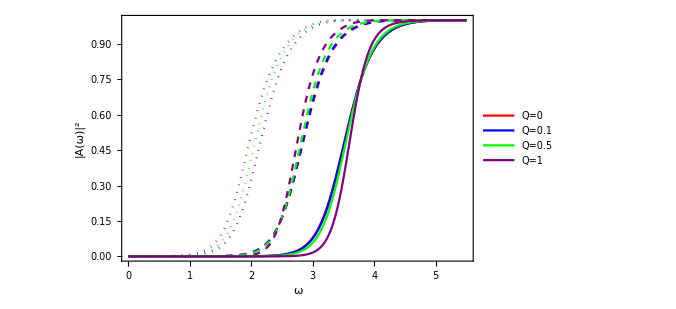

```mathematica
AbsorptionProbablities
```

```mathematica
(*Quit[];(*Always make sure this is the last command Mathematica executes*)*)
```